# Definitions

```mathematica
$Assumptions ={x∈Reals, y ∈ Reals, m ∈ Reals, Subscript[v, F] ∈ Reals,Subscript[v, F]>0, ℏ∈ Reals,ℏ>0, ϵ∈ Reals, Subscript[ϵ, 0]∈ Reals, α ∈Reals, c ∈ Reals, t ∈ Reals, a ∈ Reals, a > 0}
```

{x∈ℝ,y∈ℝ,m∈ℝ,v_F∈ℝ,v_F>0,ℏ∈ℝ,ℏ>0,ϵ∈ℝ,ϵ_0∈ℝ,α∈ℝ,c∈ℝ,t∈ℝ,a∈ℝ,a>0}

```mathematica
Subscript[σ, y] = {{0, -I}, {I, 0}}
Subscript[σ, x] = {{0, 1}, {1, 0}}
Subscript[σ, z] = {{1, 0}, {0, -1}}
```

{{0,-ⅈ},{ⅈ,0}}

{{0,1},{1,0}}

{{1,0},{0,-1}}

```mathematica
H0 = ℏ Subscript[v, F](x * Subscript[σ, y]- y * Subscript[σ, x])
```

{{0,(-ⅈ x-y) ℏ v_F},{(ⅈ x-y) ℏ v_F,0}}

```mathematica
H1 = H0 + m*Subscript[σ, z]
```

{{m,(-ⅈ x-y) ℏ v_F},{(ⅈ x-y) ℏ v_F,-m}}

# H_0 Kinetic

```mathematica
Eigenvalues[H0]
```

{-ⅈ √(-x^2-y^2) ℏ v_F,ⅈ √(-x^2-y^2) ℏ v_F}

```mathematica
Integrate[ℏ Subscript[v, F] k^2, k]
```

1/3 k^3 ℏ v_F

```mathematica
Subscript[T, 0]=(ℏ Subscript[v, F] V)/(6 π)(SubPlus[Λ]^3-SubMinus[Λ]^3)
```

(V ℏ (-Λ_-^3+Λ_+^3) v_F)/(6 π)

# H_0 Exchange

```mathematica
-V/(2 * π)*Integrate[k, {k, 0, SubMinus[Λ]-q}]
```

-(V (-q+Λ_-)^2)/(4 π)

```mathematica
Integrate[-(V (-q+SubMinus[Λ])^2)/(4 π), {q, 0, SubMinus[Λ]}]
```

-(V Λ_-^3)/(12 π)

```mathematica
Subscript[X, 0]=FullSimplify[(e^2/(4 π ϵ Subscript[ϵ, 0])) * (-(V SubMinus[Λ]^3)/(12 π)) + (e^2/(4 π ϵ Subscript[ϵ, 0])) * ((V SubPlus[Λ]^3)/(12 π))]
```

(c V α ℏ (-Λ_-^3+Λ_+^3))/(12 π ϵ)

# H_0 Total

```mathematica
FullSimplify[1/V(Subscript[T, 0]+Subscript[X, 0])]
```

-(ℏ (Λ_-^3-Λ_+^3) (c α+2 ϵ v_F))/(12 π ϵ)

```mathematica
Subscript[X, 0]/Subscript[T, 0]
```

(c α)/(2 ϵ v_F)

# H_1 Kinetic

```mathematica
Subscript[v, 0]=Normalize /@Eigenvectors[H0]
Subscript[P, 0]=Transpose[Subscript[v, 0]]
Subscript[v, 1]=Normalize /@Eigenvectors[H1]
Subscript[P, 1]=Transpose[Subscript[v, 1]]
```

{{-(√(-x^2-y^2))/((x+ⅈ y) √(1+Abs[(√(-x^2-y^2))/(x+ⅈ y)]^2)),1/(√(1+Abs[(√(-x^2-y^2))/(x+ⅈ y)]^2))},{(√(-x^2-y^2))/((x+ⅈ y) √(1+Abs[(√(-x^2-y^2))/(x+ⅈ y)]^2)),1/(√(1+Abs[(√(-x^2-y^2))/(x+ⅈ y)]^2))}}

{{-(√(-x^2-y^2))/((x+ⅈ y) √(1+Abs[(√(-x^2-y^2))/(x+ⅈ y)]^2)),(√(-x^2-y^2))/((x+ⅈ y) √(1+Abs[(√(-x^2-y^2))/(x+ⅈ y)]^2))},{1/(√(1+Abs[(√(-x^2-y^2))/(x+ⅈ y)]^2)),1/(√(1+Abs[(√(-x^2-y^2))/(x+ⅈ y)]^2))}}

{{(ⅈ (-m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2)))/((x+ⅈ y) ℏ √(1+Abs[(-m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2) v_F),1/(√(1+Abs[(-m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2))},{-(ⅈ (m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2)))/((x+ⅈ y) ℏ √(1+Abs[(m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2) v_F),1/(√(1+Abs[(m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2))}}

{{(ⅈ (-m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2)))/((x+ⅈ y) ℏ √(1+Abs[(-m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2) v_F),-(ⅈ (m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2)))/((x+ⅈ y) ℏ √(1+Abs[(m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2) v_F)},{1/(√(1+Abs[(-m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2)),1/(√(1+Abs[(m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2))}}

```mathematica
FullSimplify[First[Eigenvalues[H0]] * Conjugate[First[First[Subscript[v, 1]]]] * First[First[Subscript[v, 1]]]]
```

1/2 √(x^2+y^2) ℏ v_F (1-m/(√(m^2+(x^2+y^2) ℏ^2 v_F^2)))

```mathematica
FullSimplify[Last[Eigenvalues[H0]] * Conjugate[Last[First[Subscript[v, 1]]]] * Last[First[Subscript[v, 1]]]]
```

-1/2 √(x^2+y^2) ℏ v_F (1+m/(√(m^2+(x^2+y^2) ℏ^2 v_F^2)))

```mathematica
FullSimplify[First[Eigenvalues[H0]] * Conjugate[First[Last[Subscript[v, 1]]]] * First[Last[Subscript[v, 1]]]]
```

1/2 √(x^2+y^2) ℏ v_F (1+m/(√(m^2+(x^2+y^2) ℏ^2 v_F^2)))

```mathematica
FullSimplify[Last[Eigenvalues[H0]] * Conjugate[Last[Last[Subscript[v, 1]]]] * Last[Last[Subscript[v, 1]]]]
```

-√(x^2+y^2) ℏ v_F (1/2-m/(2 √(m^2+(x^2+y^2) ℏ^2 v_F^2)))

```mathematica
FullSimplify[1/2 √(x^2+y^2) ℏ Subscript[v, F] (1+m/(√(m^2+(x^2+y^2) ℏ^2 Subscript[v, F]^2)))+-√(x^2+y^2) ℏ Subscript[v, F] (1/2-m/(2 √(m^2+(x^2+y^2) ℏ^2 Subscript[v, F]^2)))]
```

m ℏ v_F √((x^2+y^2)/(m^2+(x^2+y^2) ℏ^2 v_F^2))

```mathematica
FullSimplify[1/2 √(x^2+y^2) ℏ Subscript[v, F] (1-m/(√(m^2+(x^2+y^2) ℏ^2 Subscript[v, F]^2)))+-1/2 √(x^2+y^2) ℏ Subscript[v, F] (1+m/(√(m^2+(x^2+y^2) ℏ^2 Subscript[v, F]^2)))]
```

-m ℏ v_F √((x^2+y^2)/(m^2+(x^2+y^2) ℏ^2 v_F^2))

```mathematica
FullSimplify[Integrate[(m k^2)/Sqrt[ℏ^2 Subscript[v, F]^2 k^2+m^2], k]]
```

(m (-m^2 ArcTanh[(k ℏ v_F)/(√(m^2+k^2 ℏ^2 v_F^2))]+k ℏ v_F √(m^2+k^2 ℏ^2 v_F^2)))/(2 ℏ^3 v_F^3)

```mathematica
Subscript[T, 1] = (V/(2 π))(m/(2 ℏ^2 Subscript[v, F]^2))(m^2 ArcTanh[(ℏ Subscript[v, F] SubMinus[Λ])/Sqrt[ℏ^2 Subscript[v, F]^2 SubMinus[Λ]^2+m^2]]-ℏ Subscript[v, F] SubMinus[Λ] Sqrt[ℏ^2 Subscript[v, F]^2 SubMinus[Λ]^2+m^2] +ℏ Subscript[v, F] SubPlus[Λ] Sqrt[ℏ^2 Subscript[v, F]^2 SubPlus[Λ]^2+m^2] -m^2 ArcTanh[(ℏ Subscript[v, F] SubPlus[Λ])/Sqrt[ℏ^2 Subscript[v, F]^2 SubPlus[Λ]^2+m^2]])
```

1/(4 π ℏ^2 v_F^2)m V (m^2 ArcTanh[(ℏ Λ_- v_F)/(√(m^2+ℏ^2 Λ_-^2 v_F^2))]-m^2 ArcTanh[(ℏ Λ_+ v_F)/(√(m^2+ℏ^2 Λ_+^2 v_F^2))]-ℏ Λ_- v_F √(m^2+ℏ^2 Λ_-^2 v_F^2)+ℏ Λ_+ v_F √(m^2+ℏ^2 Λ_+^2 v_F^2))

```mathematica
1/(4 π ℏ^2 Subscript[v, F]^2)m V (m^2 ArcTanh[(ℏ SubMinus[Λ] Subscript[v, F])/(√(m^2+ℏ^2 SubMinus[Λ]^2 Subscript[v, F]^2))]-m^2 ArcTanh[(ℏ SubPlus[Λ] Subscript[v, F])/(√(m^2+ℏ^2 SubPlus[Λ]^2 Subscript[v, F]^2))]-ℏ Λd Subscript[v, F] √(m^2+ℏ^2 SubMinus[Λ]^2 Subscript[v, F]^2)+ℏ SubPlus[Λ] Subscript[v, F] √(m^2+ℏ^2 SubPlus[Λ]^2 Subscript[v, F]^2))
```

```mathematica
Subscript[T, 1]=FullSimplify[Normal[Series[Subscript[T, 1],{Subscript[v, F],0, 3}]]]
```

(10 m^5 V ℏ (-Λ_-^3+Λ_+^3) v_F+3 m^3 V ℏ^3 (Λ_-^5-Λ_+^5) v_F^3)/(60 π Abs[m]^5)

# H_1 Exchange

```mathematica
npp=Inverse[Subscript[P, 0]].{{1, 0}, {0, 0}}.Subscript[P, 0]
npm=Inverse[Subscript[P, 0]].{{0, 1}, {0, 0}}.Subscript[P, 0]
nmp=Inverse[Subscript[P, 0]].{{0, 0}, {1, 0}}.Subscript[P, 0]
nmm=Inverse[Subscript[P, 0]].{{0, 0}, {0, 1}}.Subscript[P, 0]
```

{{1/2,-1/2},{-1/2,1/2}}

{{-(x+ⅈ y)/(2 √(-x^2-y^2)),-(x+ⅈ y)/(2 √(-x^2-y^2))},{(x+ⅈ y)/(2 √(-x^2-y^2)),(x+ⅈ y)/(2 √(-x^2-y^2))}}

{{-(√(-x^2-y^2))/(2 (x+ⅈ y)),(√(-x^2-y^2))/(2 (x+ⅈ y))},{-(√(-x^2-y^2))/(2 (x+ⅈ y)),(√(-x^2-y^2))/(2 (x+ⅈ y))}}

{{1/2,1/2},{1/2,1/2}}

```mathematica
fepp = FullSimplify[Conjugate[First[Subscript[v, 1]]].npp.First[Subscript[v, 1]]]
fepm = FullSimplify[Conjugate[First[Subscript[v, 1]]].npm.First[Subscript[v, 1]]]
femp = FullSimplify[Conjugate[First[Subscript[v, 1]]].nmp.First[Subscript[v, 1]]]
femm = FullSimplify[Conjugate[First[Subscript[v, 1]]].nmm.First[Subscript[v, 1]]]
```

1/2-(y ℏ v_F)/(2 √(m^2+(x^2+y^2) ℏ^2 v_F^2))

((-ⅈ m+x ℏ v_F) √((x^2+y^2)/(m^2+(x^2+y^2) ℏ^2 v_F^2)))/(2 (x-ⅈ y))

((ⅈ m+x ℏ v_F) √((x^2+y^2)/(m^2+(x^2+y^2) ℏ^2 v_F^2)))/(2 (x+ⅈ y))

1/2 (1+(y ℏ v_F)/(√(m^2+(x^2+y^2) ℏ^2 v_F^2)))

```mathematica
lepp = FullSimplify[Conjugate[Last[Subscript[v, 1]]].npp.Last[Subscript[v, 1]]]
lepm = FullSimplify[Conjugate[Last[Subscript[v, 1]]].npm.Last[Subscript[v, 1]]]
lemp = FullSimplify[Conjugate[Last[Subscript[v, 1]]].nmp.Last[Subscript[v, 1]]]
lemm = FullSimplify[Conjugate[Last[Subscript[v, 1]]].nmm.Last[Subscript[v, 1]]]
```

1/2 (1+(y ℏ v_F)/(√(m^2+(x^2+y^2) ℏ^2 v_F^2)))

-((-ⅈ m+x ℏ v_F) √((x^2+y^2)/(m^2+(x^2+y^2) ℏ^2 v_F^2)))/(2 (x-ⅈ y))

-((ⅈ m+x ℏ v_F) √((x^2+y^2)/(m^2+(x^2+y^2) ℏ^2 v_F^2)))/(2 (x+ⅈ y))

1/2-(y ℏ v_F)/(2 √(m^2+(x^2+y^2) ℏ^2 v_F^2))

```mathematica
Subscript[x, k]=k Cos[Subscript[θ, k]]
Subscript[y, k]=k Sin[Subscript[θ, k]]
Subscript[x, k+q]=(k+q) Cos[Subscript[θ, k+q]]
Subscript[y, k+q]=(k+q) Sin[Subscript[θ, k+q]]
```

k Cos[θ_k]

k Sin[θ_k]

(k+q) Cos[θ_(k+q)]

(k+q) Sin[θ_(k+q)]

```mathematica
FullSimplify[(1/2-(Subscript[y, k] ℏ Subscript[v, F])/(2 √(m^2+k^2 ℏ^2 Subscript[v, F]^2))) * (1/2-(Subscript[y, k+q] ℏ Subscript[v, F])/(2 √(m^2+(k+q)^2 ℏ^2 Subscript[v, F]^2))) + (1/2+(Subscript[y, k] ℏ Subscript[v, F])/(2 √(m^2+k^2 ℏ^2 Subscript[v, F]^2))) * (1/2+(Subscript[y, k+q] ℏ Subscript[v, F])/(2 √(m^2+(k+q)^2 ℏ^2 Subscript[v, F]^2))) +( ((-ⅈ m+Subscript[x, k] ℏ Subscript[v, F]) √(k^2/(m^2+k^2 ℏ^2 Subscript[v, F]^2)))/(2 (Subscript[x, k]-ⅈ Subscript[y, k]))) *( ((ⅈ m+Subscript[x, k+q] ℏ Subscript[v, F]) √((k+q)^2/(m^2+(k+q)^2 ℏ^2 Subscript[v, F]^2)))/(2 (Subscript[x, k+q]+ⅈ Subscript[y, k+q]))) + ( ((-ⅈ m+Subscript[x, k+q] ℏ Subscript[v, F]) √((k+q)^2/(m^2+(k+q)^2 ℏ^2 Subscript[v, F]^2)))/(2 (Subscript[x, k+q]-ⅈ Subscript[y, k+q]))) *( ((ⅈ m+Subscript[x, k] ℏ Subscript[v, F]) √((k)^2/(m^2+(k)^2 ℏ^2 Subscript[v, F]^2)))/(2 (Subscript[x, k]+ⅈ Subscript[y, k])))]
```

1/4 (2+(2 m^2 Cos[θ_k-θ_(k+q)] √(k^2/(m^2+k^2 ℏ^2 v_F^2)) √((k+q)^2/(m^2+(k+q)^2 ℏ^2 v_F^2)))/(k (k+q))+2 ℏ v_F ((m (-k Cos[θ_k]+(k+q) Cos[θ_(k+q)]) Sin[θ_k-θ_(k+q)] √(k^2/(m^2+k^2 ℏ^2 v_F^2)) √((k+q)^2/(m^2+(k+q)^2 ℏ^2 v_F^2)))/(k (k+q))+ℏ v_F (Cos[θ_k] Cos[θ_k-θ_(k+q)] Cos[θ_(k+q)] √(k^2/(m^2+k^2 ℏ^2 v_F^2)) √((k+q)^2/(m^2+(k+q)^2 ℏ^2 v_F^2))+(k (k+q) Sin[θ_k] Sin[θ_(k+q)])/(√(m^2+k^2 ℏ^2 v_F^2) √(m^2+(k+q)^2 ℏ^2 v_F^2)))))

```mathematica
FullSimplify[Integrate[1/4 (2+(2 m^2 Cos[Subscript[θ, k]-Subscript[θ, k+q]] √(k^2/(m^2+k^2 ℏ^2 Subscript[v, F]^2)) √((k+q)^2/(m^2+(k+q)^2 ℏ^2 Subscript[v, F]^2)))/(k (k+q))+2 ℏ Subscript[v, F] ((m (-k Cos[Subscript[θ, k]]+(k+q) Cos[Subscript[θ, k+q]]) Sin[Subscript[θ, k]-Subscript[θ, k+q]] √(k^2/(m^2+k^2 ℏ^2 Subscript[v, F]^2)) √((k+q)^2/(m^2+(k+q)^2 ℏ^2 Subscript[v, F]^2)))/(k (k+q))+ℏ Subscript[v, F] (Cos[Subscript[θ, k]] Cos[Subscript[θ, k]-Subscript[θ, k+q]] Cos[Subscript[θ, k+q]] √(k^2/(m^2+k^2 ℏ^2 Subscript[v, F]^2)) √((k+q)^2/(m^2+(k+q)^2 ℏ^2 Subscript[v, F]^2))+(k (k+q) Sin[Subscript[θ, k]] Sin[Subscript[θ, k+q]])/(√(m^2+k^2 ℏ^2 Subscript[v, F]^2) √(m^2+(k+q)^2 ℏ^2 Subscript[v, F]^2))))), {Subscript[θ, k],0, 2*π}]]
```

π+(π ℏ v_F (m Sin[θ_(k+q)]+(k+q) ℏ Cos[θ_(k+q)]^2 v_F) √(k^2/(m^2+k^2 ℏ^2 v_F^2)) √((k+q)^2/(m^2+(k+q)^2 ℏ^2 v_F^2)))/(2 (k+q))

```mathematica
FullSimplify[Integrate[π+(π ℏ Subscript[v, F] (m Sin[Subscript[θ, k+q]]+(k+q) ℏ Cos[Subscript[θ, k+q]]^2 Subscript[v, F]) √(k^2/(m^2+k^2 ℏ^2 Subscript[v, F]^2)) √((k+q)^2/(m^2+(k+q)^2 ℏ^2 Subscript[v, F]^2)))/(2 (k+q)), {Subscript[θ, k+q], 0, 2 π}]]
```

1/2 π^2 (4+ℏ^2 v_F^2 √(k^2/(m^2+k^2 ℏ^2 v_F^2)) √((k+q)^2/(m^2+(k+q)^2 ℏ^2 v_F^2)))

```mathematica
FullSimplify[Integrate[1/2 π^2 (4+ℏ^2 Subscript[v, F]^2 √(k^2/(m^2+k^2 ℏ^2 Subscript[v, F]^2)) √((k+q)^2/(m^2+(k+q)^2 ℏ^2 Subscript[v, F]^2))), q]]
```

1/2 π^2 (4 q+((k+q) √(k^2/(m^2+k^2 ℏ^2 v_F^2)))/(√((k+q)^2/(m^2+(k+q)^2 ℏ^2 v_F^2))))

```mathematica
FullSimplify[1/2 π^2 (4 (SubMinus[Λ]-k)+((k+(SubMinus[Λ]-k)) √(k^2/(m^2+k^2 ℏ^2 Subscript[v, F]^2)))/(√((k+(SubMinus[Λ]-k))^2/(m^2+(k+(SubMinus[Λ]-k))^2 ℏ^2 Subscript[v, F]^2))))-1/2 π^2 (4 0+((k+0) √(k^2/(m^2+k^2 ℏ^2 Subscript[v, F]^2)))/(√((k+0)^2/(m^2+(k+0)^2 ℏ^2 Subscript[v, F]^2))))]
```

1/2 π^2 (-5 k+4 Λ_-+(Λ_- √(k^2/(m^2+k^2 ℏ^2 v_F^2)))/(√((Λ_-^2)/(m^2+ℏ^2 Λ_-^2 v_F^2))))

```mathematica
Integrate[k*1/2 π^2 (-5 k+4 SubMinus[Λ]+(SubMinus[Λ] √(k^2/(m^2+k^2 ℏ^2 Subscript[v, F]^2)))/(√(SubMinus[Λ]^2/(m^2+ℏ^2 SubMinus[Λ]^2 Subscript[v, F]^2)))), k]
```

1/2 π^2 (-(5 k^3)/3+(Λ_- (-m^2 ArcTanh[ℏ v_F √(k^2/(m^2+k^2 ℏ^2 v_F^2))]+m^2 ℏ v_F √(k^2/(m^2+k^2 ℏ^2 v_F^2))+k^2 ℏ^3 v_F^3 (√(k^2/(m^2+k^2 ℏ^2 v_F^2))+4 √((Λ_-^2)/(m^2+ℏ^2 Λ_-^2 v_F^2)))))/(2 ℏ^3 v_F^3 √((Λ_-^2)/(m^2+ℏ^2 Λ_-^2 v_F^2))))

```mathematica
FullSimplify[1/2 π^2 (-(5 SubMinus[Λ]^3)/3+1/(2 ℏ^3 Subscript[v, F]^3 √(SubMinus[Λ]^2/(m^2+ℏ^2 SubMinus[Λ]^2 Subscript[v, F]^2)))SubMinus[Λ] (-m^2 ArcTanh[ℏ Subscript[v, F] √(SubMinus[Λ]^2/(m^2+SubMinus[Λ]^2 ℏ^2 Subscript[v, F]^2))]+m^2 ℏ Subscript[v, F] √(SubMinus[Λ]^2/(m^2+SubMinus[Λ]^2 ℏ^2 Subscript[v, F]^2))+SubMinus[Λ]^2 ℏ^3 Subscript[v, F]^3 (√(SubMinus[Λ]^2/(m^2+SubMinus[Λ]^2 ℏ^2 Subscript[v, F]^2))+4 √(SubMinus[Λ]^2/(m^2+ℏ^2 SubMinus[Λ]^2 Subscript[v, F]^2))))) - 1/2 π^2 (-(5 0^3)/3+1/(2 ℏ^3 Subscript[v, F]^3 √(SubMinus[Λ]^2/(m^2+ℏ^2 SubMinus[Λ]^2 Subscript[v, F]^2)))SubMinus[Λ] (-m^2 ArcTanh[ℏ Subscript[v, F] √(0^2/(m^2+0^2 ℏ^2 Subscript[v, F]^2))]+m^2 ℏ Subscript[v, F] √(0^2/(m^2+k^2 ℏ^2 Subscript[v, F]^2))+0^2 ℏ^3 Subscript[v, F]^3 (√(0^2/(m^2+0^2 ℏ^2 Subscript[v, F]^2))+4 √(SubMinus[Λ]^2/(m^2+ℏ^2 SubMinus[Λ]^2 Subscript[v, F]^2)))))]
```

(π^2 (3 m^2 ℏ Λ_- v_F+5 ℏ^3 Λ_-^3 v_F^3-3 m^2 ArcTanh[(ℏ Λ_- v_F)/(√(m^2+ℏ^2 Λ_-^2 v_F^2))] √(m^2+ℏ^2 Λ_-^2 v_F^2)))/(12 ℏ^3 v_F^3)

```mathematica
Subscript[X, 1]=FullSimplify[(-V/2)(e^2/(4 ϵ Subscript[ϵ, 0]))(1/(16 π^4))Normal[Series[(π^2 (3 m^2 ℏ SubMinus[Λ] Subscript[v, F]+5 ℏ^3 SubMinus[Λ]^3 Subscript[v, F]^3-3 m^2 ArcTanh[(ℏ SubMinus[Λ] Subscript[v, F])/(√(m^2+ℏ^2 SubMinus[Λ]^2 Subscript[v, F]^2))] √(m^2+ℏ^2 SubMinus[Λ]^2 Subscript[v, F]^2)))/(12 ℏ^3 Subscript[v, F]^3), {Subscript[v, F], 0, 3}]], Assumptions->{m>0, SubMinus[Λ]>0}]+FullSimplify[(-V/2)(e^2/(4 ϵ Subscript[ϵ, 0]))(1/(16 π^4))Normal[Series[(π^2 (3 m^2 ℏ SubPlus[Λ] Subscript[v, F]+5 ℏ^3 SubPlus[Λ]^3 Subscript[v, F]^3-3 m^2 ArcTanh[(ℏ SubPlus[Λ] Subscript[v, F])/(√(m^2+ℏ^2 SubPlus[Λ]^2 Subscript[v, F]^2))] √(m^2+ℏ^2 SubPlus[Λ]^2 Subscript[v, F]^2)))/(12 ℏ^3 Subscript[v, F]^3), {Subscript[v, F], 0, 3}]], Assumptions->{m>0, SubPlus[Λ]>0}]
```

-(c V α ℏ Λ_-^3 (10 m^2+ℏ^2 Λ_-^2 v_F^2))/(960 m^2 π ϵ)-(c V α ℏ Λ_+^3 (10 m^2+ℏ^2 Λ_+^2 v_F^2))/(960 m^2 π ϵ)

# H_1 Total

```mathematica
Subscript[ϵ, 0]=e^2/(4 π α ℏ c)
```

e^2/(4 c π α ℏ)

```mathematica
Subscript[E, 1]=FullSimplify[1/V(Subscript[T, 1]+Subscript[X, 1]), Assumptions->m>0]
```

(-10 c m^2 α ℏ (Λ_-^3+Λ_+^3)+160 m^2 ϵ ℏ (-Λ_-^3+Λ_+^3) v_F-c α ℏ^3 (Λ_-^5+Λ_+^5) v_F^2+48 ϵ ℏ^3 (Λ_-^5-Λ_+^5) v_F^3)/(960 m^2 π ϵ)

# Energetic Comp

```mathematica
SubMinus[Λ]=1
SubPlus[Λ]=0
```

1

0

```mathematica
Subscript[E, 1]=FullSimplify[1/V(Subscript[T, 1]+Subscript[X, 1])]
```

-(120 Abs[m]^3+640 m^3 v_F+25 Abs[m] v_F^2-192 m v_F^3)/(3840 π Abs[m]^3)

```mathematica
Subscript[E, 0] = FullSimplify[1/V(Subscript[T, 0]+Subscript[X, 0])]
```

-(3+4 v_F)/(24 π)

```mathematica
equation = Subscript[E, 1]-Subscript[E, 0]
```

(3+4 v_F)/(24 π)-(120 Abs[m]^3+640 m^3 v_F+25 Abs[m] v_F^2-192 m v_F^3)/(3840 π Abs[m]^3)

```mathematica
Solve[equation ==0, m]
```

{{m→ConditionalExpression[(√(25 v_F^2-192 v_F^3))/(6 √10), ]},{m→ConditionalExpression[-(√((25 v_F^2+192 v_F^3)/(9+32 v_F)))/(2 √10), -25/192<v_F<25/192||v_F>25/192||v_F<-9/32]}}

# High-symmetry Points

```mathematica
G1 = (2π)/a{1, -1/Sqrt[3]}
G2 = (2π)/a{0, 2/Sqrt[3]}
G3 = -G1 - G2
Subscript[κ, 1]=2/3 G1 + 1/3 G2
Subscript[κ, 3]=Subscript[κ, 1]-G1
Subscript[κ, 5]=Subscript[κ, 1]+G3
Subscript[κ, 2]=1/3 G1 + 2/3 G2
Subscript[κ, 4]=Subscript[κ, 2]+G3
Subscript[κ, 6]=Subscript[κ, 2]-G2
```

{(2 π)/a,-(2 π)/(√3 a)}

{0,(4 π)/(√3 a)}

{-(2 π)/a,-(2 π)/(√3 a)}

{(4 π)/(3 a),0}

{-(2 π)/(3 a),(2 π)/(√3 a)}

{-(2 π)/(3 a),-(2 π)/(√3 a)}

{(2 π)/(3 a),(2 π)/(√3 a)}

{-(4 π)/(3 a),0}

{(2 π)/(3 a),-(2 π)/(√3 a)}

# H_2

```mathematica
χ = FullSimplify[First[Subscript[v, 1]]]
```

{((ⅈ x+y) ℏ v_F √(1/((x^2+y^2) ℏ^2 v_F^2+m (m+√(m^2+(x^2+y^2) ℏ^2 v_F^2)))))/(√2),1/(√(2-(2 m)/(m+√(m^2+(x^2+y^2) ℏ^2 v_F^2))))}

```mathematica
Eigenvalues[H1]
```

{-√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2),√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2)}

```mathematica
Integrate[Sqrt[m^2+ℏ^2 Subscript[v, F]^2(q^2+Sqrt[Subscript[x, 1]^2+Subscript[y, 1]^2] + 2*Subscript[x, 1]*q*Cos[θ] +  2*Subscript[y, 1]*q*Sin[θ]) + m^2], θ]
```

(2 EllipticE[θ/2,(16 π q ℏ^2 v_F^2)/(6 a m^2+(3 a q^2+π (4+8 q)) ℏ^2 v_F^2)] √(6 m^2+(ℏ^2 (4 π+3 a q^2+8 π q Cos[θ]) v_F^2)/a))/(√3 √((6 a m^2+ℏ^2 (4 π+3 a q^2+8 π q Cos[θ]) v_F^2)/(6 a m^2+(3 a q^2+π (4+8 q)) ℏ^2 v_F^2)))

```mathematica
FullSimplify[(2 EllipticE[0/2,(16 π q ℏ^2 Subscript[v, F]^2)/(6 a m^2+(3 a q^2+π (4+8 q)) ℏ^2 Subscript[v, F]^2)] √(6 m^2+(ℏ^2 (4 π+3 a q^2+8 π q Cos[0]) Subscript[v, F]^2)/a))/(√3 √((6 a m^2+ℏ^2 (4 π+3 a q^2+8 π q Cos[0]) Subscript[v, F]^2)/(6 a m^2+(3 a q^2+π (4+8 q)) ℏ^2 Subscript[v, F]^2)))]
```

0

```mathematica
FullSimplify[(2 EllipticE[(2π)/2,(16 π q ℏ^2 Subscript[v, F]^2)/(6 a m^2+(3 a q^2+π (4+8 q)) ℏ^2 Subscript[v, F]^2)] √(6 m^2+(ℏ^2 (4 π+3 a q^2+8 π q Cos[2π]) Subscript[v, F]^2)/a))/(√3 √((6 a m^2+ℏ^2 (4 π+3 a q^2+8 π q Cos[2π]) Subscript[v, F]^2)/(6 a m^2+(3 a q^2+π (4+8 q)) ℏ^2 Subscript[v, F]^2)))]
```

4 EllipticE[(16 π q ℏ^2 v_F^2)/(6 a m^2+(3 a q^2+π (4+8 q)) ℏ^2 v_F^2)] √(2 m^2+((3 a q^2+π (4+8 q)) ℏ^2 v_F^2)/(3 a))

```mathematica
FullSimplify[Normal[Series[-(2 q EllipticE[ArcCsc[2/(√(2+q/(√(q^2))))],(16 π √(q^2) ℏ^2 Subscript[v, F]^2)/(6 a m^2+(3 a q^2+π (4+8 √(q^2))) ℏ^2 Subscript[v, F]^2)] √(6 m^2+((-4 π (-1+q)+3 a q^2) ℏ^2 Subscript[v, F]^2)/a))/(√3 √(q^2) √((6 a m^2+(-4 π (-1+q)+3 a q^2) ℏ^2 Subscript[v, F]^2)/(6 a m^2+(3 a q^2+π (4+8 √(q^2))) ℏ^2 Subscript[v, F]^2))), {Subscript[v, F], 0, 2}]], Assumptions->m>0]
```

(q (-4 √3 π ℏ^2 v_F^2-(2 ArcCsc[2/(√(2+q/(√(q^2))))] (12 a m^2+(4 π+3 a q^2) ℏ^2 v_F^2))/(√(q^2))))/(6 √2 a m)

```mathematica
FullSimplify[Normal[Series[4 EllipticE[(16 π q ℏ^2 Subscript[v, F]^2)/(6 a m^2+(3 a q^2+π (4+8 q)) ℏ^2 Subscript[v, F]^2)] √(2 m^2+((3 a q^2+π (4+8 q)) ℏ^2 Subscript[v, F]^2)/(3 a)), {Subscript[v, F], 0, 3}]], Assumptions->m>0]
```

(π (12 a m^2+(4 π+3 a q^2) ℏ^2 v_F^2))/(3 √2 a m)

```mathematica
(-1/(4 π^2))Integrate[q*((π (12 a m^2+(4 π+3 a q^2) ℏ^2 Subscript[v, F]^2))/(3 √2 a m)), q]
```

-(q^2 (24 a m^2+(8 π+3 a q^2) ℏ^2 v_F^2))/(48 √2 a m π)

# Form Factors

```mathematica
Subscript[x, 1]=First[Subscript[κ, 1]]
Subscript[y, 1]=Last[Subscript[κ, 1]]
Subscript[x, 3]=First[Subscript[κ, 3]]
Subscript[y, 3]=Last[Subscript[κ, 3]]
Subscript[x, 5]=First[Subscript[κ, 5]]
Subscript[y, 5]=Last[Subscript[κ, 5]]
Subscript[x, 2]=First[Subscript[κ, 2]]
Subscript[y, 2]=Last[Subscript[κ, 2]]
Subscript[x, 4]=First[Subscript[κ, 4]]
Subscript[y, 4]=Last[Subscript[κ, 4]]
Subscript[x, 6]=First[Subscript[κ, 6]]
Subscript[y, 6]=Last[Subscript[κ, 6]]
```

(4 π)/(3 a)

0

-(2 π)/(3 a)

(2 π)/(√3 a)

-(2 π)/(3 a)

-(2 π)/(√3 a)

(2 π)/(3 a)

(2 π)/(√3 a)

-(4 π)/(3 a)

0

(2 π)/(3 a)

-(2 π)/(√3 a)

```mathematica
Sqrt[Subscript[x, 1]^2+Subscript[y, 1]^2]
```

4/3 √(1/a^2) π

```mathematica
a = 1
ℏ =1
Subscript[v, F]=1
m = 1
```

1

1

1

«1 more identical outputs»

```mathematica
Clear[a, ℏ, m]
```

```mathematica
Subscript[Λ, 0]=FullSimplify[{((ⅈ Subscript[x, 1]+Subscript[y, 1]) ℏ Subscript[v, F] √(1/((Subscript[x, 1]^2+Subscript[y, 1]^2) ℏ^2 Subscript[v, F]^2+m (m+√(m^2+(Subscript[x, 1]^2+Subscript[y, 1]^2) ℏ^2 Subscript[v, F]^2)))))/(√2),1/(√(2-(2 m)/(m+√(m^2+(Subscript[x, 1]^2+Subscript[y, 1]^2) ℏ^2 Subscript[v, F]^2))))}.Conjugate[{((ⅈ Subscript[x, 3]+Subscript[y, 3]) ℏ Subscript[v, F] √(1/((Subscript[x, 3]^2+Subscript[y, 3]^2) ℏ^2 Subscript[v, F]^2+m (m+√(m^2+(Subscript[x, 3]^2+Subscript[y, 3]^2) ℏ^2 Subscript[v, F]^2)))))/(√2),1/(√(2-(2 m)/(m+√(m^2+(Subscript[x, 3]^2+Subscript[y, 3]^2) ℏ^2 Subscript[v, F]^2))))}]]
```

1/2+3/(2 √(9+16 π^2))+(4 ⅈ (ⅈ+√3) π^2)/(9+16 π^2+3 √(9+16 π^2))

```mathematica
Subscript[Λ, 1]=FullSimplify[{((ⅈ Subscript[x, 3]+Subscript[y, 3]) ℏ Subscript[v, F] √(1/((Subscript[x, 3]^2+Subscript[y, 3]^2) ℏ^2 Subscript[v, F]^2+m (m+√(m^2+(Subscript[x, 3]^2+Subscript[y, 3]^2) ℏ^2 Subscript[v, F]^2)))))/(√2),1/(√(2-(2 m)/(m+√(m^2+(Subscript[x, 3]^2+Subscript[y, 3]^2) ℏ^2 Subscript[v, F]^2))))}.Conjugate[{((ⅈ Subscript[x, 5]+Subscript[y, 5]) ℏ Subscript[v, F] √(1/((Subscript[x, 5]^2+Subscript[y, 5]^2) ℏ^2 Subscript[v, F]^2+m (m+√(m^2+(Subscript[x, 5]^2+Subscript[y, 5]^2) ℏ^2 Subscript[v, F]^2)))))/(√2),1/(√(2-(2 m)/(m+√(m^2+(Subscript[x, 5]^2+Subscript[y, 5]^2) ℏ^2 Subscript[v, F]^2))))}]]
```

(9+27/(√(9+16 π^2))+π^2 (4+4 ⅈ √3+48/(√(9+16 π^2))))/(9+16 π^2+3 √(9+16 π^2))

```mathematica
Subscript[Λ, 2]=FullSimplify[{((ⅈ Subscript[x, 5]+Subscript[y, 5]) ℏ Subscript[v, F] √(1/((Subscript[x, 5]^2+Subscript[y, 5]^2) ℏ^2 Subscript[v, F]^2+m (m+√(m^2+(Subscript[x, 5]^2+Subscript[y, 5]^2) ℏ^2 Subscript[v, F]^2)))))/(√2),1/(√(2-(2 m)/(m+√(m^2+(Subscript[x, 5]^2+Subscript[y, 5]^2) ℏ^2 Subscript[v, F]^2))))}.Conjugate[{((ⅈ Subscript[x, 1]+Subscript[y, 1]) ℏ Subscript[v, F] √(1/((Subscript[x, 1]^2+Subscript[y, 1]^2) ℏ^2 Subscript[v, F]^2+m (m+√(m^2+(Subscript[x, 1]^2+Subscript[y, 1]^2) ℏ^2 Subscript[v, F]^2)))))/(√2),1/(√(2-(2 m)/(m+√(m^2+(Subscript[x, 1]^2+Subscript[y, 1]^2) ℏ^2 Subscript[v, F]^2))))}]]
```

1/2+3/(2 √(9+16 π^2))+(4 ⅈ (ⅈ+√3) π^2)/(9+16 π^2+3 √(9+16 π^2))

```mathematica
FullSimplify[N[Arg[Subscript[Λ, 2]]]]
```

0.664801

```mathematica
FullSimplify[N[2*Arg[Subscript[Λ, 0]*Exp[-I*(G1.G1)]*Exp[I * 2(π*0)/3]]]]
```

-3.41521

```mathematica
Floor[(π - 3.415213453293334)/(2 π)]
```

-1

```mathematica
FullSimplify[N[Re[Subscript[Λ, 0]*Exp[I * 2(π*1)/3]]]]
```

-0.5

```mathematica
FullSimplify[N[Re[Subscript[Λ, 0]*Exp[I * 2(π*2)/3]]]]
```

0.0758448

```mathematica
Subscript[Λ, 0]=FullSimplify[{((ⅈ Subscript[x, 1]+Subscript[y, 1]) ℏ Subscript[v, F] √(1/((Subscript[x, 1]^2+Subscript[y, 1]^2) ℏ^2 Subscript[v, F]^2+m (m+√(m^2+(Subscript[x, 1]^2+Subscript[y, 1]^2) ℏ^2 Subscript[v, F]^2)))))/(√2),1/(√(2-(2 m)/(m+√(m^2+(Subscript[x, 1]^2+Subscript[y, 1]^2) ℏ^2 Subscript[v, F]^2))))}.Conjugate[{((ⅈ Subscript[x, 5]+Subscript[y, 5]) ℏ Subscript[v, F] √(1/((Subscript[x, 5]^2+Subscript[y, 5]^2) ℏ^2 Subscript[v, F]^2+m (m+√(m^2+(Subscript[x, 5]^2+Subscript[y, 5]^2) ℏ^2 Subscript[v, F]^2)))))/(√2),1/(√(2-(2 m)/(m+√(m^2+(Subscript[x, 5]^2+Subscript[y, 5]^2) ℏ^2 Subscript[v, F]^2))))}]]
```

1/2+3/(2 √(9+16 π^2))+((-4-4 ⅈ √3) π^2)/(9+16 π^2+3 √(9+16 π^2))

```mathematica
FullSimplify[N[Re[Subscript[Λ, 0]*Exp[I * 2(π*0)/3]]]]
```

0.424155

```mathematica
FullSimplify[N[Re[Subscript[Λ, 0]*Exp[I * 2(π*1)/3]]]]
```

0.0758448

```mathematica
FullSimplify[N[Re[Subscript[Λ, 0]*Exp[I * 2(π*2)/3]]]]
```

-0.5

# H_2 Total

```mathematica
Subscript[T, 2]=-V/(144 Sqrt[2] π a m)(24 a m^2 SubMinus[Λ]^2+ℏ^2 Subscript[v, F]^2 SubMinus[Λ]^2 (8 π + 3 a SubMinus[Λ]^2)) * g
```

-(g V (24 a m^2 Λ_-^2+ℏ^2 Λ_-^2 (8 π+3 a Λ_-^2) v_F^2))/(144 √2 a m π)

```mathematica
Subscript[H, 2]=1/(4 π^2)V * Subscript[V, 0] * n^2 * g
```

(g n^2 V V_0)/(4 π^2)

```mathematica
Subscript[F, 2] = (- e^2 V)/(16 π^2 ϵ Subscript[ϵ, 0])SubMinus[Λ]^3 *g
```

-(c g V α ℏ Λ_-^3)/(4 π ϵ)

```mathematica
Subscript[E, 2]=FullSimplify[1/V(Subscript[T, 2]+Subscript[H, 2]+Subscript[F, 2])]
```

-(g (72 a c m π α ℏ Λ_-^3+3 √2 a π ϵ ℏ^2 Λ_-^4 v_F^2+8 √2 π ϵ Λ_-^2 (3 a m^2+π ℏ^2 v_F^2)-72 a m n^2 ϵ V_0))/(288 a m π^2 ϵ)

```mathematica
Subscript[E, 1]=1/g*Subscript[E, 2]
```

-(72 a c m π α ℏ Λ_-^3+3 √2 a π ϵ ℏ^2 Λ_-^4 v_F^2+8 √2 π ϵ Λ_-^2 (3 a m^2+π ℏ^2 v_F^2)-72 a m n^2 ϵ V_0)/(288 a m π^2 ϵ)

```mathematica
Subscript[T, 11]=FullSimplify[Integrate[-q*√(m^2+ℏ^2 Subscript[v, F]^2 q^2), {q, 0, SubMinus[Λ]}], Assumptions->{m>0, SubMinus[Λ]>0}]
```

ConditionalExpression[-(-m^3+(m^2+ℏ^2 Λ_-^2 v_F^2)^(3/2))/(3 ℏ^2 v_F^2), e∈ℝ||Re[e]==0]

```mathematica
Subscript[E, 1]= FullSimplify[1/(g*V)(Subscript[H, 2]+Subscript[F, 2]) + Subscript[T, 11]]
```

ConditionalExpression[(m^3-(m^2+ℏ^2 Λ_-^2 v_F^2)^(3/2))/(3 ℏ^2 v_F^2)+(-c π α ℏ Λ_-^3+n^2 ϵ V_0)/(4 π^2 ϵ), e∈ℝ||Re[e]==0]

# Some Form Factor Computation

```mathematica
Λ[x1_, y1_, x2_, y2_]:= {((ⅈ x2+y2) ℏ Subscript[v, F] √(1/((x2^2+y2^2) ℏ^2 Subscript[v, F]^2+m (m+√(m^2+(x2^2+y2^2) ℏ^2 Subscript[v, F]^2)))))/(√2),1/(√(2-(2 m)/(m+√(m^2+(x2^2+y2^2) ℏ^2 Subscript[v, F]^2))))}.Conjugate[{((ⅈ x1+y1) ℏ Subscript[v, F] √(1/((x1^2+y1^2) ℏ^2 Subscript[v, F]^2+m (m+√(m^2+(x1^2+y1^2) ℏ^2 Subscript[v, F]^2)))))/(√2),1/(√(2-(2 m)/(m+√(m^2+(x1^2+y1^2) ℏ^2 Subscript[v, F]^2))))}]
```

# j = 0

```mathematica
L11 = FullSimplify[Λ[Subscript[x, 1],Subscript[y, 1],Subscript[x, 1],Subscript[y, 1]]]
L13 = FullSimplify[Λ[Subscript[x, 1],Subscript[y, 1],Subscript[x, 3],Subscript[y, 3]]]
L15 = FullSimplify[Λ[Subscript[x, 1],Subscript[y, 1],Subscript[x, 5],Subscript[y, 5]]]

L31 = FullSimplify[Λ[Subscript[x, 3],Subscript[y, 3],Subscript[x, 1],Subscript[y, 1]]]
L33 = FullSimplify[Λ[Subscript[x, 3],Subscript[y, 3],Subscript[x, 3],Subscript[y, 3]]]
L35 = FullSimplify[Λ[Subscript[x, 3],Subscript[y, 3],Subscript[x, 5],Subscript[y, 5]]]

L51 = FullSimplify[Λ[Subscript[x, 5],Subscript[y, 5],Subscript[x, 1],Subscript[y, 1]]]
L53 = FullSimplify[Λ[Subscript[x, 5],Subscript[y, 5],Subscript[x, 3],Subscript[y, 3]]]
L55 = FullSimplify[Λ[Subscript[x, 5],Subscript[y, 5],Subscript[x, 5],Subscript[y, 5]]]
```

Λ[(4 π)/(3 a),0,(4 π)/(3 a),0]

Λ[(4 π)/(3 a),0,-(2 π)/(3 a),(2 π)/(√3 a)]

Λ[(4 π)/(3 a),0,-(2 π)/(3 a),-(2 π)/(√3 a)]

Λ[-(2 π)/(3 a),(2 π)/(√3 a),(4 π)/(3 a),0]

Λ[-(2 π)/(3 a),(2 π)/(√3 a),-(2 π)/(3 a),(2 π)/(√3 a)]

Λ[-(2 π)/(3 a),(2 π)/(√3 a),-(2 π)/(3 a),-(2 π)/(√3 a)]

Λ[-(2 π)/(3 a),-(2 π)/(√3 a),(4 π)/(3 a),0]

Λ[-(2 π)/(3 a),-(2 π)/(√3 a),-(2 π)/(3 a),(2 π)/(√3 a)]

Λ[-(2 π)/(3 a),-(2 π)/(√3 a),-(2 π)/(3 a),-(2 π)/(√3 a)]

```mathematica
Subscript[g, 0]= FullSimplify[L11 + L13 + L15 + L31 + L33 + L35 + L51 + L53 + L55]
```

(9 Conjugate[1/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))])/(2 (9 a^2 m^2+16 π^2 ℏ^2 v_F^2)^(1/4) √(1/(6 a m+2 √(9 a^2 m^2+16 π^2 ℏ^2 v_F^2))))

```mathematica
FullSimplify[(9 (1/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 Subscript[v, F]^2)/(9 a^2)))))))/(2 (9 a^2 m^2+16 π^2 ℏ^2 Subscript[v, F]^2)^(1/4) √(1/(6 a m+2 √(9 a^2 m^2+16 π^2 ℏ^2 Subscript[v, F]^2))))]
```

9/2 (1+(3 a m)/(√(9 a^2 m^2+16 π^2 ℏ^2 v_F^2)))

# j = 1

```mathematica
L11 = FullSimplify[Λ[Subscript[x, 1],Subscript[y, 1],Subscript[x, 1],Subscript[y, 1]]]
L13 = FullSimplify[Λ[Subscript[x, 1],Subscript[y, 1],Subscript[x, 3],Subscript[y, 3]]]
L15 = FullSimplify[Λ[Subscript[x, 1],Subscript[y, 1],Subscript[x, 5],Subscript[y, 5]]]

L31 = FullSimplify[Λ[Subscript[x, 3],Subscript[y, 3],Subscript[x, 1],Subscript[y, 1]]]
L33 = FullSimplify[Λ[Subscript[x, 3],Subscript[y, 3],Subscript[x, 3],Subscript[y, 3]]]
L35 = FullSimplify[Λ[Subscript[x, 3],Subscript[y, 3],Subscript[x, 5],Subscript[y, 5]]]

L51 = FullSimplify[Λ[Subscript[x, 5],Subscript[y, 5],Subscript[x, 1],Subscript[y, 1]]]
L53 = FullSimplify[Λ[Subscript[x, 5],Subscript[y, 5],Subscript[x, 3],Subscript[y, 3]]]
L55 = FullSimplify[Λ[Subscript[x, 5],Subscript[y, 5],Subscript[x, 5],Subscript[y, 5]]]
```

```mathematica
FullSimplify[L11 + L33 + L55 + Exp[(2π I)/3*1] L31 +  Exp[(-2π I)/3*1] L13 +  Exp[(2π I)/3*1] L53 +  Exp[(-2π I)/3*1] L35 +  Exp[(2π I)/3*2] L51 + Exp[(-2π I)/3*2] L15]
```

0

# j = 2

```mathematica
FullSimplify[L11 + L33 + L55 + Exp[2*(2π I)/3*1] L31 +  Exp[2*(-2π I)/3*1] L13 +  Exp[2*(2π I)/3*1] L53 +  Exp[2*(-2π I)/3*1] L35 +  Exp[2*(2π I)/3*2] L51 + Exp[2*(-2π I)/3*2] L15]
```

72 π^2 ℏ^2 Conjugate[√(1/(16 π^2 ℏ^2 v_F^2+3 a m (3 a m+√(9 a^2 m^2+16 π^2 ℏ^2 v_F^2))))] v_F^2 √(1/(16 π^2 ℏ^2 v_F^2+3 a m (3 a m+√(9 a^2 m^2+16 π^2 ℏ^2 v_F^2))))

```mathematica
FullSimplify[72 π^2 ℏ^2 (√(1/(16 π^2 ℏ^2 Subscript[v, F]^2+3 a m (3 a m+√(9 a^2 m^2+16 π^2 ℏ^2 Subscript[v, F]^2))))) Subscript[v, F]^2 √(1/(16 π^2 ℏ^2 Subscript[v, F]^2+3 a m (3 a m+√(9 a^2 m^2+16 π^2 ℏ^2 Subscript[v, F]^2))))]
```

9/2 (1-(3 a m)/(√(9 a^2 m^2+16 π^2 ℏ^2 v_F^2)))

```mathematica
9*16*4
```

576

```mathematica
Integrate[1/Sqrt[q^2+G^2+2*q*G*Cos[θ]], {θ, 0, 2*π}]
```

ConditionalExpression[(2 EllipticK[-(4 G q)/(G-q)^2])/(√((G-q)^2))+(2 EllipticK[(4 G q)/(G+q)^2])/(√((G+q)^2)), ]

```mathematica
G = (4 π)/(a Sqrt[3])
```

(4 π)/(√3 a)

```mathematica
FullSimplify[Normal[Series[((2 EllipticK[-(4 G q)/(G-q)^2])/(√((G-q)^2))+(2 EllipticK[(4 G q)/(G+q)^2])/(√((G+q)^2))), {a, Infinity, 1}]], Assumptions->q>0]
```

(2 π)/q

```mathematica
Integrate[q*(SubMinus[Λ]-q)^2*((2 π)/q), {q, 0, SubMinus[Λ]}]
```

(2 π Λ_-^3)/3

# H_1 V2

```mathematica
FullSimplify[(1/V)*(-V/(6 π ℏ^2 Subscript[v, F]^2)(-m^3+(m^2+ℏ^2 Subscript[v, F]^2 SubMinus[Λ]^2)^(3/2)) + (-e^2 *V *SubMinus[Λ]^3)/(48 π^2 ϵ Subscript[ϵ, 0]))]
```

-((c α ℏ^3 Λ_-^3)/ϵ+(2 (-m^3+(m^2+ℏ^2 Λ_-^2 v_F^2)^(3/2)))/v_F^2)/(12 π ℏ^2)

```mathematica
Integrate[(SubMinus[Λ]-q)^2, {q, 0, SubMinus[Λ]}]
```

(Λ_-^3)/3

```mathematica
72*3
```

216

```mathematica
Integrate[q*(SubMinus[Λ]-q)^2, {q, 0, SubMinus[Λ]}]
```

(Λ_-^4)/12

```mathematica
1/36*1/24
```

1/864

```mathematica
216/27
```

8

```mathematica
L11 = FullSimplify[Λ[Subscript[x, 1],Subscript[y, 1],Subscript[x, 1],Subscript[y, 1]]]
L13 = FullSimplify[Λ[Subscript[x, 1],Subscript[y, 1],Subscript[x, 3],Subscript[y, 3]]]
L15 = FullSimplify[Λ[Subscript[x, 1],Subscript[y, 1],Subscript[x, 5],Subscript[y, 5]]]

L31 = FullSimplify[Λ[Subscript[x, 3],Subscript[y, 3],Subscript[x, 1],Subscript[y, 1]]]
L33 = FullSimplify[Λ[Subscript[x, 3],Subscript[y, 3],Subscript[x, 3],Subscript[y, 3]]]
L35 = FullSimplify[Λ[Subscript[x, 3],Subscript[y, 3],Subscript[x, 5],Subscript[y, 5]]]

L51 = FullSimplify[Λ[Subscript[x, 5],Subscript[y, 5],Subscript[x, 1],Subscript[y, 1]]]
L53 = FullSimplify[Λ[Subscript[x, 5],Subscript[y, 5],Subscript[x, 3],Subscript[y, 3]]]
L55 = FullSimplify[Λ[Subscript[x, 5],Subscript[y, 5],Subscript[x, 5],Subscript[y, 5]]]
```

(8 π^2 ℏ^2 Conjugate[√(1/((16 π^2 ℏ^2 v_F^2)/(9 a^2)+m (m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))] v_F^2 √(1/(16 π^2 ℏ^2 v_F^2+3 a m (3 a m+√(9 a^2 m^2+16 π^2 ℏ^2 v_F^2)))))/(3 a)+Conjugate[1/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))]/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))

-1/(3 a)4 ⅈ (-ⅈ+√3) π^2 ℏ^2 Conjugate[√(1/((16 π^2 ℏ^2 v_F^2)/(9 a^2)+m (m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))] v_F^2 √(1/(16 π^2 ℏ^2 v_F^2+3 a m (3 a m+√(9 a^2 m^2+16 π^2 ℏ^2 v_F^2))))+Conjugate[1/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))]/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))

(4 ⅈ (ⅈ+√3) π^2 ℏ^2 Conjugate[√(1/((16 π^2 ℏ^2 v_F^2)/(9 a^2)+m (m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))] v_F^2 √(1/(16 π^2 ℏ^2 v_F^2+3 a m (3 a m+√(9 a^2 m^2+16 π^2 ℏ^2 v_F^2)))))/(3 a)+Conjugate[1/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))]/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))

(4 ⅈ (ⅈ+√3) π^2 ℏ^2 Conjugate[√(1/((16 π^2 ℏ^2 v_F^2)/(9 a^2)+m (m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))] v_F^2 √(1/(16 π^2 ℏ^2 v_F^2+3 a m (3 a m+√(9 a^2 m^2+16 π^2 ℏ^2 v_F^2)))))/(3 a)+Conjugate[1/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))]/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))

(8 π^2 ℏ^2 Conjugate[√(1/((16 π^2 ℏ^2 v_F^2)/(9 a^2)+m (m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))] v_F^2 √(1/(16 π^2 ℏ^2 v_F^2+3 a m (3 a m+√(9 a^2 m^2+16 π^2 ℏ^2 v_F^2)))))/(3 a)+Conjugate[1/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))]/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))

-1/(3 a)2 (2+2 ⅈ √3) π^2 ℏ^2 Conjugate[√(1/((16 π^2 ℏ^2 v_F^2)/(9 a^2)+m (m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))] v_F^2 √(1/(16 π^2 ℏ^2 v_F^2+3 a m (3 a m+√(9 a^2 m^2+16 π^2 ℏ^2 v_F^2))))+Conjugate[1/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))]/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))

-1/(3 a)4 ⅈ (-ⅈ+√3) π^2 ℏ^2 Conjugate[√(1/((16 π^2 ℏ^2 v_F^2)/(9 a^2)+m (m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))] v_F^2 √(1/(16 π^2 ℏ^2 v_F^2+3 a m (3 a m+√(9 a^2 m^2+16 π^2 ℏ^2 v_F^2))))+Conjugate[1/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))]/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))

(4 ⅈ (ⅈ+√3) π^2 ℏ^2 Conjugate[√(1/((16 π^2 ℏ^2 v_F^2)/(9 a^2)+m (m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))] v_F^2 √(1/(16 π^2 ℏ^2 v_F^2+3 a m (3 a m+√(9 a^2 m^2+16 π^2 ℏ^2 v_F^2)))))/(3 a)+Conjugate[1/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))]/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))

(8 π^2 ℏ^2 Conjugate[√(1/((16 π^2 ℏ^2 v_F^2)/(9 a^2)+m (m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))] v_F^2 √(1/(16 π^2 ℏ^2 v_F^2+3 a m (3 a m+√(9 a^2 m^2+16 π^2 ℏ^2 v_F^2)))))/(3 a)+Conjugate[1/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))]/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))

```mathematica
FullSimplify[Exp[(-(2 π I))/6(2*1 - 1 - 1)] * L11 * L11 + Exp[(-(2 π I))/6(2*1 - 1 - 3)] * L11 * L31+Exp[(-(2 π I))/6(2*1 - 1 - 5)] * L11 * L51 + Exp[(-(2 π I))/6(2*1 - 3 - 1)] * L31 * L11 + Exp[(-(2 π I))/6(2*1 - 3 - 3)] * L31 * L31+Exp[(-(2 π I))/6(2*1 - 3 - 5)] * L31 * L51 + Exp[(-(2 π I))/6(2*1 - 5 - 1)] * L51 * L11 + Exp[(-(2 π I))/6(2*1 - 5 - 3)] * L51 * L31 + Exp[(-(2 π I))/6(2*1 - 5 - 5)] * L51 * L51]
```

(Conjugate[1/(√(2-(2 m)/(m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2)))))]/(√(2-(2 m)/(m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2)))))+1/2 ℏ^2 (Conjugate[x_1]+ⅈ Conjugate[y_1]) Conjugate[√(1/(ℏ^2 v_F^2 (x_1^2+y_1^2)+m (m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2)))))] v_F^2 (x_1-ⅈ y_1) √(1/(ℏ^2 v_F^2 (x_1^2+y_1^2)+m (m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2))))))^2+2 (-1)^(2/3) (Conjugate[1/(√(2-(2 m)/(m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2)))))]/(√(2-(2 m)/(m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2)))))+1/2 ℏ^2 (Conjugate[x_1]+ⅈ Conjugate[y_1]) Conjugate[√(1/(ℏ^2 v_F^2 (x_1^2+y_1^2)+m (m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2)))))] v_F^2 (x_1-ⅈ y_1) √(1/(ℏ^2 v_F^2 (x_1^2+y_1^2)+m (m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2)))))) (Conjugate[1/(√(2-(2 m)/(m+√(m^2+ℏ^2 v_F^2 (x_3^2+y_3^2)))))]/(√(2-(2 m)/(m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2)))))+1/2 ℏ^2 (Conjugate[x_3]+ⅈ Conjugate[y_3]) Conjugate[√(1/(ℏ^2 v_F^2 (x_3^2+y_3^2)+m (m+√(m^2+ℏ^2 v_F^2 (x_3^2+y_3^2)))))] v_F^2 (x_1-ⅈ y_1) √(1/(ℏ^2 v_F^2 (x_1^2+y_1^2)+m (m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2))))))-(-1)^(1/3) (Conjugate[1/(√(2-(2 m)/(m+√(m^2+ℏ^2 v_F^2 (x_3^2+y_3^2)))))]/(√(2-(2 m)/(m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2)))))+1/2 ℏ^2 (Conjugate[x_3]+ⅈ Conjugate[y_3]) Conjugate[√(1/(ℏ^2 v_F^2 (x_3^2+y_3^2)+m (m+√(m^2+ℏ^2 v_F^2 (x_3^2+y_3^2)))))] v_F^2 (x_1-ⅈ y_1) √(1/(ℏ^2 v_F^2 (x_1^2+y_1^2)+m (m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2))))))^2-2 (-1)^(1/3) (Conjugate[1/(√(2-(2 m)/(m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2)))))]/(√(2-(2 m)/(m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2)))))+1/2 ℏ^2 (Conjugate[x_1]+ⅈ Conjugate[y_1]) Conjugate[√(1/(ℏ^2 v_F^2 (x_1^2+y_1^2)+m (m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2)))))] v_F^2 (x_1-ⅈ y_1) √(1/(ℏ^2 v_F^2 (x_1^2+y_1^2)+m (m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2)))))) (Conjugate[1/(√(2-(2 m)/(m+√(m^2+ℏ^2 v_F^2 (x_5^2+y_5^2)))))]/(√(2-(2 m)/(m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2)))))+1/2 ℏ^2 (Conjugate[x_5]+ⅈ Conjugate[y_5]) Conjugate[√(1/(ℏ^2 v_F^2 (x_5^2+y_5^2)+m (m+√(m^2+ℏ^2 v_F^2 (x_5^2+y_5^2)))))] v_F^2 (x_1-ⅈ y_1) √(1/(ℏ^2 v_F^2 (x_1^2+y_1^2)+m (m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2))))))+2 (Conjugate[1/(√(2-(2 m)/(m+√(m^2+ℏ^2 v_F^2 (x_3^2+y_3^2)))))]/(√(2-(2 m)/(m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2)))))+1/2 ℏ^2 (Conjugate[x_3]+ⅈ Conjugate[y_3]) Conjugate[√(1/(ℏ^2 v_F^2 (x_3^2+y_3^2)+m (m+√(m^2+ℏ^2 v_F^2 (x_3^2+y_3^2)))))] v_F^2 (x_1-ⅈ y_1) √(1/(ℏ^2 v_F^2 (x_1^2+y_1^2)+m (m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2)))))) (Conjugate[1/(√(2-(2 m)/(m+√(m^2+ℏ^2 v_F^2 (x_5^2+y_5^2)))))]/(√(2-(2 m)/(m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2)))))+1/2 ℏ^2 (Conjugate[x_5]+ⅈ Conjugate[y_5]) Conjugate[√(1/(ℏ^2 v_F^2 (x_5^2+y_5^2)+m (m+√(m^2+ℏ^2 v_F^2 (x_5^2+y_5^2)))))] v_F^2 (x_1-ⅈ y_1) √(1/(ℏ^2 v_F^2 (x_1^2+y_1^2)+m (m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2))))))+(-1)^(2/3) (Conjugate[1/(√(2-(2 m)/(m+√(m^2+ℏ^2 v_F^2 (x_5^2+y_5^2)))))]/(√(2-(2 m)/(m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2)))))+1/2 ℏ^2 (Conjugate[x_5]+ⅈ Conjugate[y_5]) Conjugate[√(1/(ℏ^2 v_F^2 (x_5^2+y_5^2)+m (m+√(m^2+ℏ^2 v_F^2 (x_5^2+y_5^2)))))] v_F^2 (x_1-ⅈ y_1) √(1/(ℏ^2 v_F^2 (x_1^2+y_1^2)+m (m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2))))))^2

```mathematica
N[Exp[(-2*π*I*1)/6*8]*Exp[(-2*π*I)/6*8]]
```

-0.5+0.866025 ⅈ

ⅇ^(-(2 ⅈ π)/3)

```mathematica
N[ω^-1]
```

-0.5+0.866025 ⅈ

```mathematica
FullSimplify[L11 + L33 + L55 + Exp[(2π I)/3*1] L31 +  Exp[(-2π I)/3*1] L13 +  Exp[(2π I)/3*1] L53 +  Exp[(-2π I)/3*1] L35 +  Exp[(2π I)/3*2] L51 + Exp[(-2π I)/3*2] L15]
```

$Aborted

```mathematica
N[ω^-2]
```

-0.5-0.866025 ⅈ

```mathematica
N[1 + ω^-1]
```

0.5+0.866025 ⅈ

```mathematica
N[1 + ω]
```

0.5-0.866025 ⅈ

```mathematica
Integrate[Cos[θ], {θ, 0, 2π}]
```

0

```mathematica
Integrate[q*(q^2+κ^2), {q, 0, Λ}]
```

(κ^2 Λ^2)/2+Λ^4/4

```mathematica
Eigenvectors[H0]
```

{{-(√(-x^2-y^2))/(x+ⅈ y),1},{(√(-x^2-y^2))/(x+ⅈ y),1}}

```mathematica
Subscript[v, 0]
```

{{-(√(-x^2-y^2))/((x+ⅈ y) √(1+Abs[(√(-x^2-y^2))/(x+ⅈ y)]^2)),1/(√(1+Abs[(√(-x^2-y^2))/(x+ⅈ y)]^2))},{(√(-x^2-y^2))/((x+ⅈ y) √(1+Abs[(√(-x^2-y^2))/(x+ⅈ y)]^2)),1/(√(1+Abs[(√(-x^2-y^2))/(x+ⅈ y)]^2))}}

```mathematica
FullSimplify[{-(√(-x^2-y^2))/((x+ⅈ y) √(1+Abs[(√(-x^2-y^2))/(x+ⅈ y)]^2)),1/(√(1+Abs[(√(-x^2-y^2))/(x+ⅈ y)]^2))}]
```

{(-ⅈ x-y)/(√2 √(x^2+y^2)),1/(√2)}

```mathematica
L13
```

Conjugate[1/(√(2-(2 m)/(m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2)))))]/(√(2-(2 m)/(m+√(m^2+ℏ^2 v_F^2 (x_3^2+y_3^2)))))+1/2 ℏ^2 (Conjugate[x_1]+ⅈ Conjugate[y_1]) Conjugate[√(1/(ℏ^2 v_F^2 (x_1^2+y_1^2)+m (m+√(m^2+ℏ^2 v_F^2 (x_1^2+y_1^2)))))] v_F^2 (x_3-ⅈ y_3) √(1/(ℏ^2 v_F^2 (x_3^2+y_3^2)+m (m+√(m^2+ℏ^2 v_F^2 (x_3^2+y_3^2)))))

```mathematica
FullSimplify[(1/(√(2-(2 m)/(m+√(m^2+ℏ^2 Subscript[v, F]^2 (Subscript[x, 1]^2+Subscript[y, 1]^2))))))/(√(2-(2 m)/(m+√(m^2+ℏ^2 Subscript[v, F]^2 (Subscript[x, 3]^2+Subscript[y, 3]^2)))))+1/2 ℏ^2 (Subscript[x, 1]+ⅈ Subscript[y, 1]) (√(1/(ℏ^2 Subscript[v, F]^2 (Subscript[x, 1]^2+Subscript[y, 1]^2)+m (m+√(m^2+ℏ^2 Subscript[v, F]^2 (Subscript[x, 1]^2+Subscript[y, 1]^2)))))) Subscript[v, F]^2 (Subscript[x, 3]-ⅈ Subscript[y, 3]) √(1/(ℏ^2 Subscript[v, F]^2 (Subscript[x, 3]^2+Subscript[y, 3]^2)+m (m+√(m^2+ℏ^2 Subscript[v, F]^2 (Subscript[x, 3]^2+Subscript[y, 3]^2)))))]
```

$Aborted

```mathematica
N[ω^(-(0 - 1))+ω^(-(0 - 2))]
```

-1.+0. ⅈ

```mathematica
N[ω^(-2(2- 0))+ω^(-2(2 - 1))]
```

-1.+0. ⅈ

```mathematica
N[ω^2+ ω^(2*2) - (ω^1+ ω^(2*1))]
```

0.

```mathematica
N[ω^0 + ω^0 - (ω^2 + ω^4)]
```

3.+0. ⅈ

```mathematica
N[ω^2]
```

-0.5+0.866025 ⅈ

```mathematica
N[ω^0 - ω^1 ] + N[ω^0 - ω^(2*1) ]
```

3.+0. ⅈ

```mathematica
ω = Exp[2*π * I/3]
```

ⅇ^((2 ⅈ π)/3)

```mathematica
(x+I*y)(ω^-1)+(x - I*y)*(ω^-2)
```

ⅇ^((2 ⅈ π)/3) (x-ⅈ y)+ⅇ^(-(2 ⅈ π)/3) (x+ⅈ y)

```mathematica
Simplify[ⅇ^((2 ⅈ π)/3) (x-ⅈ y)+ⅇ^(-(2 ⅈ π)/3) (x+ⅈ y)]
```

-x+√3 y

```mathematica
N[1 - ω^1 + 1 - ω^2]
```

3.+0. ⅈ

```mathematica
N[ω^2+ω^4]
```

-1.+0. ⅈ

```mathematica
FullSimplify[ω^1*(x - y) + ω^2(-x - y)+ ω^2*(x - y) + ω^4(-x - y)]
```

2 y

```mathematica
Simplify[ⅇ^(-(2 ⅈ π)/3) (-x-y)+ⅇ^((2 ⅈ π)/3) (x-y)]
```

ⅈ √3 x+y

```mathematica
Integrate[Cos[θ]^2, {θ, 0, 2π}]
```

π

```mathematica
36*4/3
```

48

```mathematica
FullSimplify[L15]
```

(4 ⅈ (ⅈ+√3) π^2 ℏ^2 Conjugate[√(1/((16 π^2 ℏ^2 v_F^2)/(9 a^2)+m (m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))] v_F^2 √(1/(16 π^2 ℏ^2 v_F^2+3 a m (3 a m+√(9 a^2 m^2+16 π^2 ℏ^2 v_F^2)))))/(3 a)+Conjugate[1/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))]/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))

```mathematica
FullSimplify[1/(3 a)4 ⅈ (ⅈ+√3) π^2 ℏ^2 (√(1/((16 π^2 ℏ^2 Subscript[v, F]^2)/(9 a^2)+m (m+√(m^2+(16 π^2 ℏ^2 Subscript[v, F]^2)/(9 a^2)))))) Subscript[v, F]^2 √(1/(16 π^2 ℏ^2 Subscript[v, F]^2+3 a m (3 a m+√(9 a^2 m^2+16 π^2 ℏ^2 Subscript[v, F]^2))))+(1/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 Subscript[v, F]^2)/(9 a^2))))))/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 Subscript[v, F]^2)/(9 a^2)))))]
```

1/2+(3 a m)/(2 √(9 a^2 m^2+16 π^2 ℏ^2 v_F^2))+(4 ⅈ (ⅈ+√3) π^2 ℏ^2 v_F^2)/(16 π^2 ℏ^2 v_F^2+3 a m (3 a m+√(9 a^2 m^2+16 π^2 ℏ^2 v_F^2)))

```mathematica
FullSimplify[L51]
```

-1/(3 a)4 ⅈ (-ⅈ+√3) π^2 ℏ^2 Conjugate[√(1/((16 π^2 ℏ^2 v_F^2)/(9 a^2)+m (m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))] v_F^2 √(1/(16 π^2 ℏ^2 v_F^2+3 a m (3 a m+√(9 a^2 m^2+16 π^2 ℏ^2 v_F^2))))+Conjugate[1/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))]/(√(2-(2 m)/(m+√(m^2+(16 π^2 ℏ^2 v_F^2)/(9 a^2)))))

```mathematica
FullSimplify[Subscript[v, 0]]
```

{{(-ⅈ x-y)/(√2 √(x^2+y^2)),1/(√2)},{(√(-x^2-y^2))/(√2 (x+ⅈ y)),1/(√2)}}

```mathematica
FullSimplify[Subscript[v, 1]]
```

{{((ⅈ x+y) ℏ v_F √(1/((x^2+y^2) ℏ^2 v_F^2+m (m+√(m^2+(x^2+y^2) ℏ^2 v_F^2)))))/(√2),1/(√(2-(2 m)/(m+√(m^2+(x^2+y^2) ℏ^2 v_F^2))))},{((-ⅈ x-y) ℏ v_F √(1/((x^2+y^2) ℏ^2 v_F^2+m (m-√(m^2+(x^2+y^2) ℏ^2 v_F^2)))))/(√2),1/(√(2+(2 m)/(-m+√(m^2+(x^2+y^2) ℏ^2 v_F^2))))}}

```mathematica
FullSimplify[{0,1/(√(2-(2 m)/(m+√(m^2+0 ℏ^2 Subscript[v, F]^2))))}]
```

{0,(√(1+Sign[m]))/(√2)}

```mathematica
FullSimplify[Λ[x, y, 0, 0]]
```

Piecewise[{{Conjugate[1/(√(2-(2 m)/(m+√(m^2+(x^2+y^2) ℏ^2 v_F^2))))], m>0}, {1/2, m==0}, {0, True}}]

```mathematica
Subscript[v, 1]
```

{{(ⅈ (-m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2)))/((x+ⅈ y) ℏ √(1+Abs[(-m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2) v_F),1/(√(1+Abs[(-m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2))},{-(ⅈ (m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2)))/((x+ⅈ y) ℏ √(1+Abs[(m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2) v_F),1/(√(1+Abs[(m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2))}}

```mathematica
FullSimplify[First[Subscript[v, 1]], Assumptions->m<0]
```

{(ⅈ (-m+√(m^2+(x^2+y^2) ℏ^2 v_F^2)))/((x+ⅈ y) ℏ √(1+Abs[(-m+√(m^2+(x^2+y^2) ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2) v_F),1/(√(1+Abs[(-m+√(m^2+(x^2+y^2) ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2))}

```mathematica
FullSimplify[{(ⅈ (-m+√(m^2+(x^2+y^2) ℏ^2 Subscript[v, F]^2)))/((x+ⅈ y) ℏ √(1+Conjugate[(-m+√(m^2+(x^2+y^2) ℏ^2 Subscript[v, F]^2))/((x+ⅈ y) ℏ Subscript[v, F])]*((-m+√(m^2+(x^2+y^2) ℏ^2 Subscript[v, F]^2))/((x+ⅈ y) ℏ Subscript[v, F]))) Subscript[v, F]),1/(√(1+Conjugate[(-m+√(m^2+(x^2+y^2) ℏ^2 Subscript[v, F]^2))/((x+ⅈ y) ℏ Subscript[v, F])]*((-m+√(m^2+(x^2+y^2) ℏ^2 Subscript[v, F]^2))/((x+ⅈ y) ℏ Subscript[v, F]))))}]
```

{(ⅈ (-m+√(m^2+(x^2+y^2) ℏ^2 v_F^2)))/((x+ⅈ y) √(2 ℏ^2 v_F^2+(2 m (m-√(m^2+(x^2+y^2) ℏ^2 v_F^2)))/(x^2+y^2))),1/(√(2-(2 m)/(m+√(m^2+(x^2+y^2) ℏ^2 v_F^2))))}

```mathematica
FullSimplify[{(ⅈ (-m+√(m^2+0* ℏ^2 Subscript[v, F]^2)))/(0* √(2 ℏ^2 Subscript[v, F]^2+(2 m (m-√(m^2+0* ℏ^2 Subscript[v, F]^2)))/(x^2+y^2))),1/(√(2-(2 m)/(m+√(m^2+0* ℏ^2 Subscript[v, F]^2))))}]
```

Power::infy: Infinite expression 1/0 encountered.

{ComplexInfinity,(√(1+Sign[m]))/(√2)}

```mathematica
First[Subscript[v, 1]]
```

{(ⅈ (-m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2)))/((x+ⅈ y) ℏ √(1+Abs[(-m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2) v_F),1/(√(1+Abs[(-m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2))}

```mathematica
FullSimplify[{(ⅈ (-m+√(m^2+x^2 ℏ^2 Subscript[v, F]^2+y^2 ℏ^2 Subscript[v, F]^2)))/((x+ⅈ y) ℏ √(1+((-m+√(m^2+x^2 ℏ^2 Subscript[v, F]^2+y^2 ℏ^2 Subscript[v, F]^2))/((x+ⅈ y) ℏ Subscript[v, F]))*Conjugate[(-m+√(m^2+x^2 ℏ^2 Subscript[v, F]^2+y^2 ℏ^2 Subscript[v, F]^2))/((x+ⅈ y) ℏ Subscript[v, F])]) Subscript[v, F]),1/(√(1+((-m+√(m^2+x^2 ℏ^2 Subscript[v, F]^2+y^2 ℏ^2 Subscript[v, F]^2))/((x+ⅈ y) ℏ Subscript[v, F]))*Conjugate[(-m+√(m^2+x^2 ℏ^2 Subscript[v, F]^2+y^2 ℏ^2 Subscript[v, F]^2))/((x+ⅈ y) ℏ Subscript[v, F])]))}]
```

{(ⅈ (-m+√(m^2+(x^2+y^2) ℏ^2 v_F^2)))/((x+ⅈ y) √(2 ℏ^2 v_F^2+(2 m (m-√(m^2+(x^2+y^2) ℏ^2 v_F^2)))/(x^2+y^2))),1/(√(2-(2 m)/(m+√(m^2+(x^2+y^2) ℏ^2 v_F^2))))}

```mathematica
Simplify[{(ⅈ (-m+√(m^2)))/(√(0+2 m (m-√(m^2)))),1/(√(2-(2 m)/(m+√(m^2))))}]
```

{Piecewise[{{ⅈ, m<0}, {0, True}}],Piecewise[{{1, m≥0}, {0, True}}]}

```mathematica
Λ[x1_, y1_, x2_, y2_]:= {(ⅈ (-m+√(m^2+(x1^2+y1^2) ℏ^2 Subscript[v, F]^2)))/((x1+ⅈ y1) √(2 ℏ^2 Subscript[v, F]^2+(2 m (m-√(m^2+(x1^2+y1^2) ℏ^2 Subscript[v, F]^2)))/(x1^2+y1^2))),1/(√(2-(2 m)/(m+√(m^2+(x1^2+y1^2) ℏ^2 Subscript[v, F]^2))))}.Conjugate[{(ⅈ (-m+√(m^2+(x2^2+y2^2) ℏ^2 Subscript[v, F]^2)))/((x2+ⅈ y2) √(2 ℏ^2 Subscript[v, F]^2+(2 m (m-√(m^2+(x2^2+y2^2) ℏ^2 Subscript[v, F]^2)))/(x2^2+y2^2))),1/(√(2-(2 m)/(m+√(m^2+(x2^2+y2^2) ℏ^2 Subscript[v, F]^2))))}]
```

```mathematica
FullSimplify[{(ⅈ (-m+√(m^2+x^2 ℏ^2 Subscript[v, F]^2+y^2 ℏ^2 Subscript[v, F]^2)))/((x+ⅈ y) ℏ √(1+((-m+√(m^2+x^2 ℏ^2 Subscript[v, F]^2+y^2 ℏ^2 Subscript[v, F]^2))/((x+ⅈ y) ℏ Subscript[v, F]))*Conjugate[(-m+√(m^2+x^2 ℏ^2 Subscript[v, F]^2+y^2 ℏ^2 Subscript[v, F]^2))/((x+ⅈ y) ℏ Subscript[v, F])]) Subscript[v, F]),1/(√(1+((-m+√(m^2+x^2 ℏ^2 Subscript[v, F]^2+y^2 ℏ^2 Subscript[v, F]^2))/((x+ⅈ y) ℏ Subscript[v, F]))*Conjugate[(-m+√(m^2+x^2 ℏ^2 Subscript[v, F]^2+y^2 ℏ^2 Subscript[v, F]^2))/((x+ⅈ y) ℏ Subscript[v, F])]))}]
```

{(ⅈ (-m+√(m^2+(x^2+y^2) ℏ^2 v_F^2)))/((x+ⅈ y) √(2 ℏ^2 v_F^2+(2 m (m-√(m^2+(x^2+y^2) ℏ^2 v_F^2)))/(x^2+y^2))),1/(√(2-(2 m)/(m+√(m^2+(x^2+y^2) ℏ^2 v_F^2))))}

```mathematica
Λ[0, 0, x, y]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
vec1 = 1/Sqrt[2*(Sqrt[(ℏ Subscript[v, F] Sqrt[x^2+y^2])^2+m^2])*(m + Sqrt[(ℏ Subscript[v, F] Sqrt[x^2+y^2])^2+m^2])]{-I*ℏ Subscript[v, F] y - ℏ Subscript[v, F] x,m + Sqrt[(ℏ Subscript[v, F] Sqrt[x^2+y^2])^2+m^2]}
```

{(-x ℏ v_F-ⅈ y ℏ v_F)/(√2 √(√(m^2+(x^2+y^2) ℏ^2 v_F^2) (m+√(m^2+(x^2+y^2) ℏ^2 v_F^2)))),(m+√(m^2+(x^2+y^2) ℏ^2 v_F^2))/(√2 √(√(m^2+(x^2+y^2) ℏ^2 v_F^2) (m+√(m^2+(x^2+y^2) ℏ^2 v_F^2))))}

```mathematica
FullSimplify[{0/(√2 √(√(m^2+(x^2+y^2) ℏ^2 Subscript[v, F]^2) (m+√(m^2+(x^2+y^2) ℏ^2 Subscript[v, F]^2)))),(m+√(m^2+0 ℏ^2 Subscript[v, F]^2))/(√2 √(√(m^2+0 ℏ^2 Subscript[v, F]^2) (m+√(m^2+0 ℏ^2 Subscript[v, F]^2))))}.Conjugate[{(-x ℏ Subscript[v, F]-ⅈ y ℏ Subscript[v, F])/(√2 √(√(m^2+(x^2+y^2) ℏ^2 Subscript[v, F]^2) (m+√(m^2+(x^2+y^2) ℏ^2 Subscript[v, F]^2)))),(m+√(m^2+(x^2+y^2) ℏ^2 Subscript[v, F]^2))/(√2 √(√(m^2+(x^2+y^2) ℏ^2 Subscript[v, F]^2) (m+√(m^2+(x^2+y^2) ℏ^2 Subscript[v, F]^2))))}], Assumptions->m<0]
```

FullSimplify::infd: Expression ((m+√(m^2)) Conjugate[(m+√(m^2+Plus[«2»] Power[«2»] Power[«2»]))/(√(√(Power[«2»]+Times[«3»]) (m+√Plus[«2»])))])/(2 √(√(m^2) (m+√(m^2)))) simplified to Indeterminate.

Indeterminate

```mathematica
Normalize /@Eigenvectors[H0 - Subscript[σ, z]]
```

{{(ⅈ (1+√(1+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2)))/((x+ⅈ y) ℏ √(1+Abs[(1+√(1+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2) v_F),1/(√(1+Abs[(1+√(1+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2))},{-(ⅈ (-1+√(1+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2)))/((x+ⅈ y) ℏ √(1+Abs[(-1+√(1+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2) v_F),1/(√(1+Abs[(-1+√(1+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2))}}

```mathematica
FullSimplify[{-(ⅈ (-1+√(1+x^2 ℏ^2 Subscript[v, F]^2+y^2 ℏ^2 Subscript[v, F]^2)))/((x+ⅈ y) ℏ √(1+((-1+√(1+x^2 ℏ^2 Subscript[v, F]^2+y^2 ℏ^2 Subscript[v, F]^2))/((x+ⅈ y) ℏ Subscript[v, F]))*Conjugate[(-1+√(1+x^2 ℏ^2 Subscript[v, F]^2+y^2 ℏ^2 Subscript[v, F]^2))/((x+ⅈ y) ℏ Subscript[v, F])]) Subscript[v, F]),1/(√(1+((-1+√(1+x^2 ℏ^2 Subscript[v, F]^2+y^2 ℏ^2 Subscript[v, F]^2))/((x+ⅈ y) ℏ Subscript[v, F]))*Conjugate[(-1+√(1+x^2 ℏ^2 Subscript[v, F]^2+y^2 ℏ^2 Subscript[v, F]^2))/((x+ⅈ y) ℏ Subscript[v, F])]))}]
```

{-(ⅈ (-1+√(1+(x^2+y^2) ℏ^2 v_F^2)))/((x+ⅈ y) √((2+2 (x^2+y^2) ℏ^2 v_F^2-2 √(1+(x^2+y^2) ℏ^2 v_F^2))/(x^2+y^2))),(√(1+1/(√(1+(x^2+y^2) ℏ^2 v_F^2))))/(√2)}

```mathematica
Eigenvectors[m*Subscript[σ, z]]
```

{{0,1},{1,0}}

```mathematica
First[Subscript[v, 1]]
```

{(ⅈ (-m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2)))/((x+ⅈ y) ℏ √(1+Abs[(-m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2) v_F),1/(√(1+Abs[(-m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2))}

```mathematica
Limit[Limit[Λ[0, 0, x, y], x->0], y->0]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

Piecewise[{{1, m≥0}, {0, True}}]

```mathematica
PiecewiseExpand[Piecewise[{{1,m≥0}},0]]
```

Piecewise[{{1, m≥0}, {0, True}}]

```mathematica
Eigenvalues[-Subscript[σ, z]]
```

{-1,1}

```mathematica
Eigenvectors[-Subscript[σ, z]]
```

{{1,0},{0,1}}

```mathematica
Subscript[v, 1]
```

{{(ⅈ (-m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2)))/((x+ⅈ y) ℏ √(1+Abs[(-m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2) v_F),1/(√(1+Abs[(-m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2))},{-(ⅈ (m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2)))/((x+ⅈ y) ℏ √(1+Abs[(m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2) v_F),1/(√(1+Abs[(m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2))}}

```mathematica
Eigenvalues[H1]
```

{-√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2),√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2)}

```mathematica
Subscript[v, 1]
```

{{(ⅈ (-m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2)))/((x+ⅈ y) ℏ √(1+Abs[(-m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2) v_F),1/(√(1+Abs[(-m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2))},{-(ⅈ (m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2)))/((x+ⅈ y) ℏ √(1+Abs[(m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2) v_F),1/(√(1+Abs[(m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2))/((x+ⅈ y) ℏ v_F)]^2))}}

```mathematica
Eigenvectors[H0 + m*Subscript[σ, z]]
```

{{(ⅈ (-m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2)))/((x+ⅈ y) ℏ v_F),1},{-(ⅈ (m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2)))/((x+ⅈ y) ℏ v_F),1}}

```mathematica
Eigenvalues[H0 + m*Subscript[σ, z]]
```

{-√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2),√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2)}

```mathematica
Eigenvectors[H0 - m*Subscript[σ, z]]
```

{{(ⅈ (m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2)))/((x+ⅈ y) ℏ v_F),1},{-(ⅈ (-m+√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2)))/((x+ⅈ y) ℏ v_F),1}}

```mathematica
Eigenvalues[H0 - m*Subscript[σ, z]]
```

{-√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2),√(m^2+x^2 ℏ^2 v_F^2+y^2 ℏ^2 v_F^2)}

```mathematica
Subscript[v, temp]=FullSimplify[Normalize /@Eigenvectors[H0+m*Subscript[σ, z]]]
```

{{((ⅈ x+y) ℏ v_F √(1/((x^2+y^2) ℏ^2 v_F^2+m (m+√(m^2+(x^2+y^2) ℏ^2 v_F^2)))))/(√2),1/(√(2-(2 m)/(m+√(m^2+(x^2+y^2) ℏ^2 v_F^2))))},{((-ⅈ x-y) ℏ v_F √(1/((x^2+y^2) ℏ^2 v_F^2+m (m-√(m^2+(x^2+y^2) ℏ^2 v_F^2)))))/(√2),1/(√(2+(2 m)/(-m+√(m^2+(x^2+y^2) ℏ^2 v_F^2))))}}

```mathematica
Subscript[v, temp]=FullSimplify[Normalize /@Eigenvectors[H0-m*Subscript[σ, z]]]
```

{{((ⅈ x+y) ℏ v_F √(1/((x^2+y^2) ℏ^2 v_F^2+m (m-√(m^2+(x^2+y^2) ℏ^2 v_F^2)))))/(√2),1/(√(2+(2 m)/(-m+√(m^2+(x^2+y^2) ℏ^2 v_F^2))))},{((-ⅈ x-y) ℏ v_F √(1/((x^2+y^2) ℏ^2 v_F^2+m (m+√(m^2+(x^2+y^2) ℏ^2 v_F^2)))))/(√2),1/(√(2-(2 m)/(m+√(m^2+(x^2+y^2) ℏ^2 v_F^2))))}}

```mathematica
gam[γ_]:= 1/2{1 - γ, 1 + γ}
```

```mathematica
χ[x_, y_, γ_]:= 1/Sqrt[2 * Sqrt[ℏ^2 Subscript[v, F]^2 (x^2+y^2)+m^2] * (γ * Abs[m] + Sqrt[ℏ^2 Subscript[v, F]^2 (x^2+y^2)+m^2])]{I*ℏ*Subscript[v, F]*x + ℏ*Subscript[v, F]*y, γ*Abs[m] + Sqrt[ℏ^2 Subscript[v, F]^2 (x^2+y^2)+m^2]}
```

```mathematica
FullSimplify[Conjugate[χ[x1, y1, 1]].χ[x2, y2, 1]]
```

(Conjugate[1/(√(m^2+(x1^2+y1^2) ℏ^2 v_F^2+Abs[m] √(m^2+(x1^2+y1^2) ℏ^2 v_F^2)))] (m^2+(x2-ⅈ y2) ℏ^2 (Conjugate[x1]+ⅈ Conjugate[y1]) v_F^2+Abs[m] √(m^2+(x2^2+y2^2) ℏ^2 v_F^2)+Conjugate[√(m^2+(x1^2+y1^2) ℏ^2 v_F^2)] (Abs[m]+√(m^2+(x2^2+y2^2) ℏ^2 v_F^2))))/(2 √(m^2+(x2^2+y2^2) ℏ^2 v_F^2+Abs[m] √(m^2+(x2^2+y2^2) ℏ^2 v_F^2)))

```mathematica
FullSimplify[((1/(√(m^2+(x1^2+y1^2) ℏ^2 Subscript[v, F]^2+Abs[m] √(m^2+(x1^2+y1^2) ℏ^2 Subscript[v, F]^2)))) (m^2+(x2-ⅈ y2) ℏ^2 (x1+ⅈ y1) Subscript[v, F]^2+Abs[m] √(m^2+(x2^2+y2^2) ℏ^2 Subscript[v, F]^2)+(√(m^2+(x1^2+y1^2) ℏ^2 Subscript[v, F]^2)) (Abs[m]+√(m^2+(x2^2+y2^2) ℏ^2 Subscript[v, F]^2))))/(2 √(m^2+(x2^2+y2^2) ℏ^2 Subscript[v, F]^2+Abs[m] √(m^2+(x2^2+y2^2) ℏ^2 Subscript[v, F]^2)))]
```

(m^2+(x1+ⅈ y1) (x2-ⅈ y2) ℏ^2 v_F^2+Abs[m] √(m^2+(x2^2+y2^2) ℏ^2 v_F^2)+√(m^2+(x1^2+y1^2) ℏ^2 v_F^2) (Abs[m]+√(m^2+(x2^2+y2^2) ℏ^2 v_F^2)))/(2 √(m^2+(x1^2+y1^2) ℏ^2 v_F^2+Abs[m] √(m^2+(x1^2+y1^2) ℏ^2 v_F^2)) √(m^2+(x2^2+y2^2) ℏ^2 v_F^2+Abs[m] √(m^2+(x2^2+y2^2) ℏ^2 v_F^2)))

```mathematica
FullSimplify[Conjugate[χ[x1, y1, -1]].χ[x2, y2, -1]]
```

(Conjugate[1/(√(m^2+(x1^2+y1^2) ℏ^2 v_F^2-Abs[m] √(m^2+(x1^2+y1^2) ℏ^2 v_F^2)))] (m^2+(x2-ⅈ y2) ℏ^2 (Conjugate[x1]+ⅈ Conjugate[y1]) v_F^2-Abs[m] √(m^2+(x2^2+y2^2) ℏ^2 v_F^2)+Conjugate[√(m^2+(x1^2+y1^2) ℏ^2 v_F^2)] (-Abs[m]+√(m^2+(x2^2+y2^2) ℏ^2 v_F^2))))/(2 √(m^2+(x2^2+y2^2) ℏ^2 v_F^2-Abs[m] √(m^2+(x2^2+y2^2) ℏ^2 v_F^2)))

```mathematica
FullSimplify[((1/(√(m^2+(x1^2+y1^2) ℏ^2 Subscript[v, F]^2-Abs[m] √(m^2+(x1^2+y1^2) ℏ^2 Subscript[v, F]^2)))) (m^2+(x2-ⅈ y2) ℏ^2 (x1+ⅈ y1) Subscript[v, F]^2-Abs[m] √(m^2+(x2^2+y2^2) ℏ^2 Subscript[v, F]^2)+(√(m^2+(x1^2+y1^2) ℏ^2 Subscript[v, F]^2)) (-Abs[m]+√(m^2+(x2^2+y2^2) ℏ^2 Subscript[v, F]^2))))/(2 √(m^2+(x2^2+y2^2) ℏ^2 Subscript[v, F]^2-Abs[m] √(m^2+(x2^2+y2^2) ℏ^2 Subscript[v, F]^2)))]
```

(m^2+(x1+ⅈ y1) (x2-ⅈ y2) ℏ^2 v_F^2-Abs[m] √(m^2+(x2^2+y2^2) ℏ^2 v_F^2)+√(m^2+(x1^2+y1^2) ℏ^2 v_F^2) (-Abs[m]+√(m^2+(x2^2+y2^2) ℏ^2 v_F^2)))/(2 √(m^2+(x1^2+y1^2) ℏ^2 v_F^2-Abs[m] √(m^2+(x1^2+y1^2) ℏ^2 v_F^2)) √(m^2+(x2^2+y2^2) ℏ^2 v_F^2-Abs[m] √(m^2+(x2^2+y2^2) ℏ^2 v_F^2)))

```mathematica
FullSimplify[(0+Abs[m] √(m^2+(x2^2+y2^2) ℏ^2 Subscript[v, F]^2)+√(m^2+(x1^2+y1^2) ℏ^2 Subscript[v, F]^2) (Abs[m]+√(m^2+(x2^2+y2^2) ℏ^2 Subscript[v, F]^2)))/(2 √(m^2+(x1^2+y1^2) ℏ^2 Subscript[v, F]^2+Abs[m] √(m^2+(x1^2+y1^2) ℏ^2 Subscript[v, F]^2)) √(m^2+(x2^2+y2^2) ℏ^2 Subscript[v, F]^2+Abs[m] √(m^2+(x2^2+y2^2) ℏ^2 Subscript[v, F]^2)))]
```

(Abs[m] √(m^2+(x2^2+y2^2) ℏ^2 v_F^2)+√(m^2+(x1^2+y1^2) ℏ^2 v_F^2) (Abs[m]+√(m^2+(x2^2+y2^2) ℏ^2 v_F^2)))/(2 √(m^2+(x1^2+y1^2) ℏ^2 v_F^2+Abs[m] √(m^2+(x1^2+y1^2) ℏ^2 v_F^2)) √(m^2+(x2^2+y2^2) ℏ^2 v_F^2+Abs[m] √(m^2+(x2^2+y2^2) ℏ^2 v_F^2)))

```mathematica
FullSimplify[(0-Abs[m] √(m^2+(x2^2+y2^2) ℏ^2 Subscript[v, F]^2)+√(m^2+(x1^2+y1^2) ℏ^2 Subscript[v, F]^2) (-Abs[m]+√(m^2+(x2^2+y2^2) ℏ^2 Subscript[v, F]^2)))/(2 √(m^2+(x1^2+y1^2) ℏ^2 Subscript[v, F]^2-Abs[m] √(m^2+(x1^2+y1^2) ℏ^2 Subscript[v, F]^2)) √(m^2+(x2^2+y2^2) ℏ^2 Subscript[v, F]^2-Abs[m] √(m^2+(x2^2+y2^2) ℏ^2 Subscript[v, F]^2)))]
```

(-Abs[m] √(m^2+(x2^2+y2^2) ℏ^2 v_F^2)+√(m^2+(x1^2+y1^2) ℏ^2 v_F^2) (-Abs[m]+√(m^2+(x2^2+y2^2) ℏ^2 v_F^2)))/(2 √(m^2+(x1^2+y1^2) ℏ^2 v_F^2-Abs[m] √(m^2+(x1^2+y1^2) ℏ^2 v_F^2)) √(m^2+(x2^2+y2^2) ℏ^2 v_F^2-Abs[m] √(m^2+(x2^2+y2^2) ℏ^2 v_F^2)))

```mathematica
FullSimplify[Conjugate[χ[Subscript[k, x], Subscript[k, y], 1]].χ[Subscript[q, x], Subscript[q, y], 1]]
```

(Conjugate[1/(√(m^2+ℏ^2 (k_x^2+k_y^2) v_F^2+Abs[m] √(m^2+ℏ^2 (k_x^2+k_y^2) v_F^2)))] (m^2+ℏ^2 (Conjugate[k_x]+ⅈ Conjugate[k_y]) (q_x-ⅈ q_y) v_F^2+Abs[m] √(m^2+ℏ^2 (q_x^2+q_y^2) v_F^2)+Conjugate[√(m^2+ℏ^2 (k_x^2+k_y^2) v_F^2)] (Abs[m]+√(m^2+ℏ^2 (q_x^2+q_y^2) v_F^2))))/(2 √(m^2+ℏ^2 (q_x^2+q_y^2) v_F^2+Abs[m] √(m^2+ℏ^2 (q_x^2+q_y^2) v_F^2)))

```mathematica
FullSimplify[((1/(√(m^2+ℏ^2 k^2 Subscript[v, F]^2+Abs[m] √(m^2+ℏ^2 k^2 Subscript[v, F]^2)))) (m^2+ℏ^2 (Subscript[k, x]+ⅈ Subscript[k, y]) (Subscript[q, x]-ⅈ Subscript[q, y]) Subscript[v, F]^2+Abs[m] √(m^2+ℏ^2 q^2 Subscript[v, F]^2)+(√(m^2+ℏ^2 k^2 Subscript[v, F]^2)) (Abs[m]+√(m^2+ℏ^2 q^2 Subscript[v, F]^2))))/(2 √(m^2+ℏ^2 q^2 Subscript[v, F]^2+Abs[m] √(m^2+ℏ^2 q^2 Subscript[v, F]^2)))]
```

(m^2+ℏ^2 (k_x+ⅈ k_y) (q_x-ⅈ q_y) v_F^2+Abs[m] √(m^2+q^2 ℏ^2 v_F^2)+√(m^2+k^2 ℏ^2 v_F^2) (Abs[m]+√(m^2+q^2 ℏ^2 v_F^2)))/(2 √(m^2+k^2 ℏ^2 v_F^2+Abs[m] √(m^2+k^2 ℏ^2 v_F^2)) √(m^2+q^2 ℏ^2 v_F^2+Abs[m] √(m^2+q^2 ℏ^2 v_F^2)))

```mathematica
FullSimplify[((m^2+ℏ^2 (Subscript[x, 1]+ⅈ Subscript[y, 1]) (Subscript[x, 3]-ⅈ Subscript[y, 3]) Subscript[v, F]^2+γ*Abs[m] √(m^2+g^2 ℏ^2 Subscript[v, F]^2)+√(m^2+g^2 ℏ^2 Subscript[v, F]^2) (γ *Abs[m]+√(m^2+g^2 ℏ^2 Subscript[v, F]^2)))/(2 √(m^2+g^2 ℏ^2 Subscript[v, F]^2+γ *Abs[m] √(m^2+g^2 ℏ^2 Subscript[v, F]^2)) √(m^2+g^2 ℏ^2 Subscript[v, F]^2+γ *Abs[m] √(m^2+g^2 ℏ^2 Subscript[v, F]^2))))*((m^2+ℏ^2 (Subscript[x, 4]+ⅈ Subscript[y, 4]) (Subscript[x, 6]-ⅈ Subscript[y, 6]) Subscript[v, F]^2+γ*Abs[m] √(m^2+g^2 ℏ^2 Subscript[v, F]^2)+√(m^2+g^2 ℏ^2 Subscript[v, F]^2) (γ *Abs[m]+√(m^2+g^2 ℏ^2 Subscript[v, F]^2)))/(2 √(m^2+g^2 ℏ^2 Subscript[v, F]^2+γ *Abs[m] √(m^2+g^2 ℏ^2 Subscript[v, F]^2)) √(m^2+g^2 ℏ^2 Subscript[v, F]^2+γ *Abs[m] √(m^2+g^2 ℏ^2 Subscript[v, F]^2))))]
```

(((9 a^2 g^2+(-8-8 ⅈ √3) π^2) ℏ^2 v_F^2+18 a^2 (m^2+γ Abs[m] √(m^2+g^2 ℏ^2 v_F^2)))^2)/(324 a^4 (m^2+g^2 ℏ^2 v_F^2+γ Abs[m] √(m^2+g^2 ℏ^2 v_F^2))^2)

```mathematica
g = Norm[Subscript[κ, 1]]
```

(4 π)/(3 Abs[a])

```mathematica
FullSimplify[(((9 a^2 g^2+(-8-8 ⅈ √3) π^2) ℏ^2 Subscript[v, F]^2+18 a^2 (m^2+γ Abs[m] √(m^2+g^2 ℏ^2 Subscript[v, F]^2)))^2)/(324 a^4 (m^2+g^2 ℏ^2 Subscript[v, F]^2+γ Abs[m] √(m^2+g^2 ℏ^2 Subscript[v, F]^2))^2)]
```

(((4-4 ⅈ √3) π^2 ℏ^2 v_F^2+3 a (3 a m^2+γ Abs[m] √(9 a^2 m^2+16 π^2 ℏ^2 v_F^2)))^2)/((16 π^2 ℏ^2 v_F^2+3 a (3 a m^2+γ Abs[m] √(9 a^2 m^2+16 π^2 ℏ^2 v_F^2)))^2)

```mathematica
Clear[g]
```

```mathematica
FullSimplify[(((4-4 ⅈ √3) π^2 ℏ^2 Subscript[v, F]^2 + x)^2)/((16 π^2 ℏ^2 Subscript[v, F]^2+x)^2), Assumptions->x∈Reals]
```

((x+(4-4 ⅈ √3) π^2 ℏ^2 v_F^2)^2)/((x+16 π^2 ℏ^2 v_F^2)^2)

```mathematica
FullSimplify[((m^2+ℏ^2 (Subscript[x, 1]+ⅈ Subscript[y, 1]) (Subscript[x, 2]-ⅈ Subscript[y, 2]) Subscript[v, F]^2+γ*Abs[m] √(m^2+g^2 ℏ^2 Subscript[v, F]^2)+√(m^2+g^2 ℏ^2 Subscript[v, F]^2) (γ *Abs[m]+√(m^2+g^2 ℏ^2 Subscript[v, F]^2)))/(2 √(m^2+g^2 ℏ^2 Subscript[v, F]^2+γ *Abs[m] √(m^2+g^2 ℏ^2 Subscript[v, F]^2)) √(m^2+g^2 ℏ^2 Subscript[v, F]^2+γ *Abs[m] √(m^2+g^2 ℏ^2 Subscript[v, F]^2))))*((m^2+ℏ^2 (Subscript[x, 4]+ⅈ Subscript[y, 4]) (Subscript[x, 5]-ⅈ Subscript[y, 5]) Subscript[v, F]^2+γ*Abs[m] √(m^2+g^2 ℏ^2 Subscript[v, F]^2)+√(m^2+g^2 ℏ^2 Subscript[v, F]^2) (γ *Abs[m]+√(m^2+g^2 ℏ^2 Subscript[v, F]^2)))/(2 √(m^2+g^2 ℏ^2 Subscript[v, F]^2+γ *Abs[m] √(m^2+g^2 ℏ^2 Subscript[v, F]^2)) √(m^2+g^2 ℏ^2 Subscript[v, F]^2+γ *Abs[m] √(m^2+g^2 ℏ^2 Subscript[v, F]^2))))]
```

((4 (3-ⅈ √3) π^2 ℏ^2 v_F^2+3 a (3 a m^2+γ Abs[m] √(9 a^2 m^2+16 π^2 ℏ^2 v_F^2)))^2)/((16 π^2 ℏ^2 v_F^2+3 a (3 a m^2+γ Abs[m] √(9 a^2 m^2+16 π^2 ℏ^2 v_F^2)))^2)

```mathematica
FullSimplify[(ℏ^2 Subscript[v, F]^2 g^2)/(2 (m^2+ℏ^2 Subscript[v, F]^2 g^2-Sqrt[m^4+ℏ^2 Subscript[v, F]^2 g^2 m^2]))*(γ+1)/2+1/2(1 + Abs[m]/Sqrt[m^2+ℏ^2 Subscript[v, F]^2 g^2])(1-γ)/2]
```

(8 π^2 ℏ^2 v_F^2)/(9 a^2 m^2+16 π^2 ℏ^2 v_F^2-3 a Abs[m] √(9 a^2 m^2+16 π^2 ℏ^2 v_F^2))

```mathematica
FullSimplify[(x + 4*(1 - I*Sqrt[3]) * π^2 ℏ^2 Subscript[v, F]^2)^2]
```

(x+(4-4 ⅈ √3) π^2 ℏ^2 v_F^2)^2

```mathematica
Expand[(x+(4-4 ⅈ √3) π^2 ℏ^2 Subscript[v, F]^2)^2]
```

x^2+8 π^2 x ℏ^2 v_F^2-8 ⅈ √3 π^2 x ℏ^2 v_F^2-32 π^4 ℏ^4 v_F^4-32 ⅈ √3 π^4 ℏ^4 v_F^4

```mathematica
FullSimplify[(x^2+8 π^2 ℏ^2 Subscript[v, F]^2 x - 32 π^4 ℏ^4 Subscript[v, F]^4)/((x + 16 π^2 ℏ^2 Subscript[v, F]^2)^2)]
```

(x^2+8 π^2 x ℏ^2 v_F^2-32 π^4 ℏ^4 v_F^4)/((x+16 π^2 ℏ^2 v_F^2)^2)

```mathematica
Expand[(x+4(3-ⅈ √3) π^2 ℏ^2 Subscript[v, F]^2)^2]
```

x^2+24 π^2 x ℏ^2 v_F^2-8 ⅈ √3 π^2 x ℏ^2 v_F^2+96 π^4 ℏ^4 v_F^4-96 ⅈ √3 π^4 ℏ^4 v_F^4

```mathematica
f[γ_]:= 3 a(3 a m^2+γ Abs[m] Sqrt[9 a^2 m^2 + 16 π^2 ℏ^2 Subscript[v, F]^2])
```

```mathematica
EH = FullSimplify[2*(f[γ]^2+8 π^2 ℏ^2 Subscript[v, F]^2 f[γ] - 32 π^4 ℏ^4 Subscript[v, F]^4)/(3 (f[γ] + 16 π^2 ℏ^2 Subscript[v, F]^2)^2)Cos[2 π/3(C0)] + 2*(8Sqrt[3] π^2 ℏ^2 Subscript[v, F]^2 f[γ] + 32 Sqrt[3] π^4 ℏ^4 Subscript[v, F]^4)/(3 (f[γ] + 16 π^2 ℏ^2 Subscript[v, F]^2)^2)Sin[2 π/3(C0)]]
```

(64 π^4 ℏ^4 (-Cos[(2 C0 π)/3]+√3 Sin[(2 C0 π)/3]) v_F^4+54 a^3 m Cos[(2 C0 π)/3] (3 a m^3 (1+γ^2)+2 m γ Abs[m] √(9 a^2 m^2+16 π^2 ℏ^2 v_F^2))+48 a π^2 ℏ^2 v_F^2 (3 a m^2 ((1+2 γ^2) Cos[(2 C0 π)/3]+√3 Sin[(2 C0 π)/3])+γ Abs[m] (Cos[(2 C0 π)/3]+√3 Sin[(2 C0 π)/3]) √(9 a^2 m^2+16 π^2 ℏ^2 v_F^2)))/(3 (16 π^2 ℏ^2 v_F^2+3 a (3 a m^2+γ Abs[m] √(9 a^2 m^2+16 π^2 ℏ^2 v_F^2)))^2)

```mathematica
FullSimplify[Normal[Series[EH, {Subscript[v, F], 0, 3}]]]
```

2/27 (9 Cos[(2 C0 π)/3]+(8 π^2 ℏ^2 (-3 Cos[(2 C0 π)/3]+√3 Sin[(2 C0 π)/3]) v_F^2)/(a^2 m^2 (1+γ)))

```mathematica
EF = FullSimplify[-2*(f[γ]^2+24 π^2 ℏ^2 Subscript[v, F]^2 f[γ] +96 π^4 ℏ^4 Subscript[v, F]^4)/(3 (f[γ] + 16 π^2 ℏ^2 Subscript[v, F]^2)^2)Cos[2 π/3(C0)] + 2*(8Sqrt[3] π^2 ℏ^2 Subscript[v, F]^2 f[γ] + 96 Sqrt[3] π^4 ℏ^4 Subscript[v, F]^4)/(3 (f[γ] + 16 π^2 ℏ^2 Subscript[v, F]^2)^2)Sin[2 π/3(C0)]]
```

-((2 (32 π^4 ℏ^4 (Cos[(2 C0 π)/3]-√3 Sin[(2 C0 π)/3]) v_F^4+9 a^3 m Cos[(2 C0 π)/3] (3 a m^3 (1+γ^2)+2 m γ Abs[m] √(9 a^2 m^2+16 π^2 ℏ^2 v_F^2))+8 a π^2 ℏ^2 v_F^2 (3 a m^2 ((3+2 γ^2) Cos[(2 C0 π)/3]-√3 Sin[(2 C0 π)/3])+γ Abs[m] (3 Cos[(2 C0 π)/3]-√3 Sin[(2 C0 π)/3]) √(9 a^2 m^2+16 π^2 ℏ^2 v_F^2))))/(16 π^2 ℏ^2 v_F^2+3 a (3 a m^2+γ Abs[m] √(9 a^2 m^2+16 π^2 ℏ^2 v_F^2)))^2)

```mathematica
a = 1
ℏ = 1
m = 0.1
γ= 1
C0 = 0
```

```mathematica
Clear[a, ℏ, m, γ, C0]
```

```mathematica
Clear[C0]
```

```mathematica
C0=0
```

0

```mathematica
Energy0 = EF + EH
```

(-0.12-69268.7 v_F^4-0.4 √(0.09+157.914 v_F^2)+v_F^2 (-263.189-526.379 √(0.09+157.914 v_F^2)))/((0.3+526.379 v_F^2+1. √(0.09+157.914 v_F^2))^2)+(0.12-23089.6 v_F^4+0.4 √(0.09+157.914 v_F^2)+v_F^2 (157.914+175.46 √(0.09+157.914 v_F^2)))/((0.3+526.379 v_F^2+1. √(0.09+157.914 v_F^2))^2)

```mathematica
C0=1
```

1

```mathematica
Energy1 = EF + EH
```

(46179.1 v_F^4+1/2 (-0.12-0.4 √(0.09+157.914 v_F^2))+v_F^2 (1/2 (-157.914-175.46 √(0.09+157.914 v_F^2))+1/2 √3 (91.1715+303.905 √(0.09+157.914 v_F^2))))/(0.3+526.379 v_F^2+1. √(0.09+157.914 v_F^2))^2+(138537. v_F^4+1/2 (0.12+0.4 √(0.09+157.914 v_F^2))+v_F^2 (1/2 √3 (91.1715+303.905 √(0.09+157.914 v_F^2))+1/2 (263.189+526.379 √(0.09+157.914 v_F^2))))/(0.3+526.379 v_F^2+1. √(0.09+157.914 v_F^2))^2

```mathematica
C0 = 2
```

2

```mathematica
Energy2 = EF+EH
```

(-23089.6 v_F^4+1/2 (-0.12-0.4 √(0.09+157.914 v_F^2))+v_F^2 (1/2 (-157.914-175.46 √(0.09+157.914 v_F^2))-1/2 √3 (91.1715+303.905 √(0.09+157.914 v_F^2))))/(0.3+526.379 v_F^2+1. √(0.09+157.914 v_F^2))^2+(-69268.7 v_F^4+1/2 (0.12+0.4 √(0.09+157.914 v_F^2))+v_F^2 (-1/2 √3 (91.1715+303.905 √(0.09+157.914 v_F^2))+1/2 (263.189+526.379 √(0.09+157.914 v_F^2))))/(0.3+526.379 v_F^2+1. √(0.09+157.914 v_F^2))^2

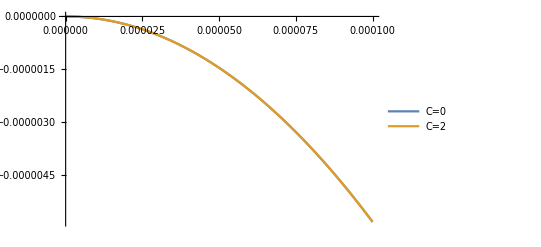

```mathematica
Plot[{Energy0, Energy2}, {Subscript[v, F], 0, 0.0001}, PlotLegends->{"C=0", "C=2"}]
```

```mathematica
FullSimplify[Conjugate[χ[Subscript[k, x], Subscript[k, y], -1]].χ[Subscript[q, x], Subscript[q, y], -1]]
```

(Conjugate[1/(√(m^2+ℏ^2 (k_x^2+k_y^2) v_F^2-Abs[m] √(m^2+ℏ^2 (k_x^2+k_y^2) v_F^2)))] (m^2+ℏ^2 (Conjugate[k_x]+ⅈ Conjugate[k_y]) (q_x-ⅈ q_y) v_F^2-Abs[m] √(m^2+ℏ^2 (q_x^2+q_y^2) v_F^2)+Conjugate[√(m^2+ℏ^2 (k_x^2+k_y^2) v_F^2)] (-Abs[m]+√(m^2+ℏ^2 (q_x^2+q_y^2) v_F^2))))/(2 √(m^2+ℏ^2 (q_x^2+q_y^2) v_F^2-Abs[m] √(m^2+ℏ^2 (q_x^2+q_y^2) v_F^2)))

```mathematica
FullSimplify[((1/(√(m^2+ℏ^2 (Subscript[k, x]^2+Subscript[k, y]^2) Subscript[v, F]^2-Abs[m] √(m^2+ℏ^2 (Subscript[k, x]^2+Subscript[k, y]^2) Subscript[v, F]^2)))) (m^2+ℏ^2 (Subscript[k, x]+ⅈ Subscript[k, y]) (Subscript[q, x]-ⅈ Subscript[q, y]) Subscript[v, F]^2-Abs[m] √(m^2+ℏ^2 (Subscript[q, x]^2+Subscript[q, y]^2) Subscript[v, F]^2)+(√(m^2+ℏ^2 (Subscript[k, x]^2+Subscript[k, y]^2) Subscript[v, F]^2)) (-Abs[m]+√(m^2+ℏ^2 (Subscript[q, x]^2+Subscript[q, y]^2) Subscript[v, F]^2))))/(2 √(m^2+ℏ^2 (Subscript[q, x]^2+Subscript[q, y]^2) Subscript[v, F]^2-Abs[m] √(m^2+ℏ^2 (Subscript[q, x]^2+Subscript[q, y]^2) Subscript[v, F]^2)))]
```

(m^2+ℏ^2 (k_x+ⅈ k_y) (q_x-ⅈ q_y) v_F^2-Abs[m] √(m^2+ℏ^2 (q_x^2+q_y^2) v_F^2)+√(m^2+ℏ^2 (k_x^2+k_y^2) v_F^2) (-Abs[m]+√(m^2+ℏ^2 (q_x^2+q_y^2) v_F^2)))/(2 √(m^2+ℏ^2 (k_x^2+k_y^2) v_F^2-Abs[m] √(m^2+ℏ^2 (k_x^2+k_y^2) v_F^2)) √(m^2+ℏ^2 (q_x^2+q_y^2) v_F^2-Abs[m] √(m^2+ℏ^2 (q_x^2+q_y^2) v_F^2)))